```mathematica
sx={{0,1},{1,0}}/2
```

{{0,1/2},{1/2,0}}

```mathematica
sy={{0,-I},{I,0}}/2
```

{{0,-ⅈ/2},{ⅈ/2,0}}

```mathematica
sz={{1,0},{0,-1}}/2
```

{{1/2,0},{0,-1/2}}

```mathematica
e= {{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
{{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
z={{0,0},{0,0}}
```

{{0,0},{0,0}}

```mathematica
Sza = TensorProduct[sz,e]//ArrayFlatten
```

{{1/2,0,0,0},{0,1/2,0,0},{0,0,-1/2,0},{0,0,0,-1/2}}

```mathematica
Szb= TensorProduct[e, sz]//ArrayFlatten
```

{{1/2,0,0,0},{0,-1/2,0,0},{0,0,1/2,0},{0,0,0,-1/2}}

```mathematica
Sxa=TensorProduct[sx,e]//ArrayFlatten
```

{{0,0,1/2,0},{0,0,0,1/2},{1/2,0,0,0},{0,1/2,0,0}}

```mathematica
Sxb= TensorProduct[e, sx]//ArrayFlatten
```

{{0,1/2,0,0},{1/2,0,0,0},{0,0,0,1/2},{0,0,1/2,0}}

```mathematica
Sya=TensorProduct[sy,e]//ArrayFlatten
```

{{0,0,-ⅈ/2,0},{0,0,0,-ⅈ/2},{ⅈ/2,0,0,0},{0,ⅈ/2,0,0}}

```mathematica
Syb= TensorProduct[e, sy]//ArrayFlatten
```

{{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0},{0,0,0,-ⅈ/2},{0,0,ⅈ/2,0}}

```mathematica
EE= TensorProduct[e, e]/2//ArrayFlatten
```

{{1/2,0,0,0},{0,1/2,0,0},{0,0,1/2,0},{0,0,0,1/2}}

```mathematica
ZZ= TensorProduct[z, z]//ArrayFlatten
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
SxSx=2TensorProduct[sx,sx]//ArrayFlatten
```

{{0,0,0,1/2},{0,0,1/2,0},{0,1/2,0,0},{1/2,0,0,0}}

```mathematica
SxSy=2TensorProduct[sx,sy]//ArrayFlatten
```

{{0,0,0,-ⅈ/2},{0,0,ⅈ/2,0},{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0}}

```mathematica
SxSz=2TensorProduct[sx,sz]//ArrayFlatten
```

{{0,0,1/2,0},{0,0,0,-1/2},{1/2,0,0,0},{0,-1/2,0,0}}

```mathematica
SySx=2TensorProduct[sy,sx]//ArrayFlatten
```

{{0,0,0,-ⅈ/2},{0,0,-ⅈ/2,0},{0,ⅈ/2,0,0},{ⅈ/2,0,0,0}}

```mathematica
SySy=2TensorProduct[sy,sy]//ArrayFlatten
```

{{0,0,0,-1/2},{0,0,1/2,0},{0,1/2,0,0},{-1/2,0,0,0}}

```mathematica
SySz=2TensorProduct[sy,sz]//ArrayFlatten
```

{{0,0,-ⅈ/2,0},{0,0,0,ⅈ/2},{ⅈ/2,0,0,0},{0,-ⅈ/2,0,0}}

```mathematica
SzSx=2TensorProduct[sz,sx]//ArrayFlatten
```

{{0,1/2,0,0},{1/2,0,0,0},{0,0,0,-1/2},{0,0,-1/2,0}}

```mathematica
SzSy=2TensorProduct[sz,sy]//ArrayFlatten
```

{{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0},{0,0,0,ⅈ/2},{0,0,-ⅈ/2,0}}

```mathematica
SzSz=2TensorProduct[sz,sz]//ArrayFlatten
```

{{1/2,0,0,0},{0,-1/2,0,0},{0,0,-1/2,0},{0,0,0,1/2}}

```mathematica
(* S1= {Sxa, Sya,Sza} *)
```

```mathematica
(* S2= {Sxb, Syb,Szb} *)
```

```mathematica
ProductBasis = {EE, Sxa,Sya,Sza,Sxb,Syb,Szb,SxSx,SxSy,SxSz,SySx,SySy,SySz,SzSx,SzSy,SzSz}
```

{{{1/2,0,0,0},{0,1/2,0,0},{0,0,1/2,0},{0,0,0,1/2}},{{0,0,1/2,0},{0,0,0,1/2},{1/2,0,0,0},{0,1/2,0,0}},{{0,0,-ⅈ/2,0},{0,0,0,-ⅈ/2},{ⅈ/2,0,0,0},{0,ⅈ/2,0,0}},{{1/2,0,0,0},{0,1/2,0,0},{0,0,-1/2,0},{0,0,0,-1/2}},{{0,1/2,0,0},{1/2,0,0,0},{0,0,0,1/2},{0,0,1/2,0}},{{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0},{0,0,0,-ⅈ/2},{0,0,ⅈ/2,0}},{{1/2,0,0,0},{0,-1/2,0,0},{0,0,1/2,0},{0,0,0,-1/2}},{{0,0,0,1/2},{0,0,1/2,0},{0,1/2,0,0},{1/2,0,0,0}},{{0,0,0,-ⅈ/2},{0,0,ⅈ/2,0},{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0}},{{0,0,1/2,0},{0,0,0,-1/2},{1/2,0,0,0},{0,-1/2,0,0}},{{0,0,0,-ⅈ/2},{0,0,-ⅈ/2,0},{0,ⅈ/2,0,0},{ⅈ/2,0,0,0}},{{0,0,0,-1/2},{0,0,1/2,0},{0,1/2,0,0},{-1/2,0,0,0}},{{0,0,-ⅈ/2,0},{0,0,0,ⅈ/2},{ⅈ/2,0,0,0},{0,-ⅈ/2,0,0}},{{0,1/2,0,0},{1/2,0,0,0},{0,0,0,-1/2},{0,0,-1/2,0}},{{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0},{0,0,0,ⅈ/2},{0,0,-ⅈ/2,0}},{{1/2,0,0,0},{0,-1/2,0,0},{0,0,-1/2,0},{0,0,0,1/2}}}

```mathematica
(* ProductBasisAlpha = {"EE", "S1x","S1y","S1z","S2x","S2y","S2z","S1xS2x","S1xS2y","S1xS2z","S1yS2x","S1yS2y","S1yS2z","S1zS2x","S1zS2y","S1zS2z"} *)
```

```mathematica
ProductBasisAlpha = {"EE", "Sxa","Sya","Sza","Sxb","Syb","Szb","SxSx","SxSy","SxSz","SySx","SySy","SySz","SzSx","SzSy","SzSz"}
```

{EE,Sxa,Sya,Sza,Sxb,Syb,Szb,SxSx,SxSy,SxSz,SySx,SySy,SySz,SzSx,SzSy,SzSz}

```mathematica
ProductBasisIndex=Table[i, {i,Length[ProductBasis]}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
MatrixTrace[a_]:= Module[{sum=0,i}, For[i=1,i<=Length[a[[1]]], i++, sum=sum+a[[i,i]]]; sum]
```

```mathematica
BasisProject[a_]:=Module[{i,out=Table[0, {i,Length[ProductBasis]}]}, For[i=1,i<= Length[ProductBasis],i++, out[[i]]=MatrixTrace[ProductBasis[[i]].a]]; out]
```

```mathematica
BasisProjectAlpha[a_] :=Simplify[ BasisProject[a].ProductBasisAlpha]
```

```mathematica
comm[a_,b_]:= a.b-b.a
```

```mathematica
cComm[a_,b_]:= comm[a,comm[a,b]]
```

```mathematica
PropagateBaseOp[a_,b_, ξ_]:= Module[{index=BasisProject[b].ProductBasisIndex, out= ZZ},If[Simplify[comm[a,b]]==ZZ,out=a,out=MatrixExp[-I*ξ*b].a.MatrixExp[I*ξ*b]; out= ExpToTrig[out]];TrigReduce[out]]
```

```mathematica
PropagateOp[a_,b_, ξ_]:= Module[{prop=ZZ, coff=0},For[i=1,i<=16,i++, coff=BasisProject[a][[i]];If[ToString[coff]!="0",  prop= prop+coff*PropagateBaseOp[ProductBasis[[i]],b,ξ]]]; prop]
```

```mathematica
rho0=EE-(SxSx+SySy+SzSz)/2 (* Q_S = 1/4 - S_a.S_b; EE/2 omitted! *)
```

```mathematica
rho0=(EE-SxSx+Sxa-Sxb)/2
```

{{1/4,-1/4,1/4,-1/4},{-1/4,1/4,-1/4,1/4},{1/4,-1/4,1/4,-1/4},{-1/4,1/4,-1/4,1/4}}

```mathematica
rho0A=BasisProjectAlpha[rho0]
```

1/2 (EE+Sxa-Sxb-SxSx)

```mathematica
(* H0a= Sza*Omegaa+ Szb*Omegab+ dmJ*SzSz- dp2J*(SxSx+SySy) *)
```

```mathematica
(* Eigensystem[H0a] *)
```

```mathematica
(* Reorder= {{0,1,0,0}, {0,0,0,1},{0,0,1,0},{1,0,0,0}} *)
```

```mathematica
(* H0aEVa//FullSimplify *)
```

```mathematica
(* H0aEVaR=Reorder.H0aEVa//FullSimplify *)
```

```mathematica
(* H0aEVeR=Reorder.H0aEVe *)
```

```mathematica
(* H0=q(Sza-Szb)+ dmJ*SzSz *) (* ω_s(Sza+Szb) omitted *)
```

```mathematica
rho0e=PropagateOp[rho0,(SxSy-SySx), ξ/2]//FullSimplify
```

{{1/4,1/4 (-Cos[ξ/2]+Sin[ξ/2]),1/4 (Cos[ξ/2]+Sin[ξ/2]),-1/4},{1/4 (-Cos[ξ/2]+Sin[ξ/2]),1/4 (1-Sin[ξ]),-Cos[ξ]/4,1/4 (Cos[ξ/2]-Sin[ξ/2])},{1/4 (Cos[ξ/2]+Sin[ξ/2]),-Cos[ξ]/4,1/4 (1+Sin[ξ]),1/4 (-Cos[ξ/2]-Sin[ξ/2])},{-1/4,1/4 (Cos[ξ/2]-Sin[ξ/2]),1/4 (-Cos[ξ/2]-Sin[ξ/2]),1/4}}

```mathematica
BasisProjectAlpha[rho0e]//FullSimplify
```

1/4 (2 EE-SxSx+SySy+2 (Sxa-Sxb) Cos[ξ/2]-(SxSx+SySy) Cos[ξ]+2 (SxSz+SzSx) Sin[ξ/2]+(-Sza+Szb) Sin[ξ])

```mathematica
rho1e=PropagateOp[rho0e,Sza-Szb,q*t]//FullSimplify
```

{{1/4,1/4 ⅇ^(ⅈ q t) (-Cos[ξ/2]+Sin[ξ/2]),1/4 ⅇ^(-ⅈ q t) (Cos[ξ/2]+Sin[ξ/2]),-1/4},{1/4 ⅇ^(-ⅈ q t) (-Cos[ξ/2]+Sin[ξ/2]),1/4 (1-Sin[ξ]),-1/4 ⅇ^(-2 ⅈ q t) Cos[ξ],1/4 ⅇ^(-ⅈ q t) (Cos[ξ/2]-Sin[ξ/2])},{1/4 ⅇ^(ⅈ q t) (Cos[ξ/2]+Sin[ξ/2]),-1/4 ⅇ^(2 ⅈ q t) Cos[ξ],1/4 (1+Sin[ξ]),-1/4 ⅇ^(ⅈ q t) (Cos[ξ/2]+Sin[ξ/2])},{-1/4,1/4 ⅇ^(ⅈ q t) (Cos[ξ/2]-Sin[ξ/2]),-1/4 ⅇ^(-ⅈ q t) (Cos[ξ/2]+Sin[ξ/2]),1/4}}

```mathematica
BasisProjectAlpha[rho1e]//FullSimplify
```

1/4 (2 EE-SxSx+SySy-(SxSx+SySy) Cos[2 q t] Cos[ξ]+2 Cos[ξ/2] (Cos[dmJ t] ((Sxa-Sxb) Cos[q t]+(Sya+Syb) Sin[q t])+Sin[dmJ t] ((SySz-SzSy) Cos[q t]-(SxSz+SzSx) Sin[q t]))+(SxSy-SySx) Cos[ξ] Sin[2 q t]+2 (Sin[dmJ t] ((Sya+Syb) Cos[q t]+(-Sxa+Sxb) Sin[q t])+Cos[dmJ t] ((SxSz+SzSx) Cos[q t]+(SySz-SzSy) Sin[q t])) Sin[ξ/2]+(-Sza+Szb) Sin[ξ])

```mathematica
rho1e=PropagateOp[rho1e,SzSz,dmJ*t]//FullSimplify
```

{{1/4,1/4 ⅇ^(-ⅈ (dmJ-q) t) (-Cos[ξ/2]+Sin[ξ/2]),1/4 ⅇ^(-ⅈ (dmJ+q) t) (Cos[ξ/2]+Sin[ξ/2]),-1/4},{1/4 ⅇ^(ⅈ (dmJ-q) t) (-Cos[ξ/2]+Sin[ξ/2]),1/4 (1-Sin[ξ]),-1/4 ⅇ^(-2 ⅈ q t) Cos[ξ],1/4 ⅇ^(ⅈ (dmJ-q) t) (Cos[ξ/2]-Sin[ξ/2])},{1/4 ⅇ^(ⅈ (dmJ+q) t) (Cos[ξ/2]+Sin[ξ/2]),-1/4 ⅇ^(2 ⅈ q t) Cos[ξ],1/4 (1+Sin[ξ]),-1/4 ⅇ^(ⅈ (dmJ+q) t) (Cos[ξ/2]+Sin[ξ/2])},{-1/4,1/4 ⅇ^(-ⅈ (dmJ-q) t) (Cos[ξ/2]-Sin[ξ/2]),-1/4 ⅇ^(-ⅈ (dmJ+q) t) (Cos[ξ/2]+Sin[ξ/2]),1/4}}

```mathematica
BasisProjectAlpha[rho1e]//FullSimplify
```

1/4 (2 EE-SxSx+SySy-(SxSx+SySy) Cos[2 q t] Cos[ξ]+2 Cos[ξ/2] (Cos[dmJ t] ((Sxa-Sxb) Cos[q t]+(Sya+Syb) Sin[q t])+Sin[dmJ t] ((SySz-SzSy) Cos[q t]-(SxSz+SzSx) Sin[q t]))+(SxSy-SySx) Cos[ξ] Sin[2 q t]+2 (Sin[dmJ t] ((Sya+Syb) Cos[q t]+(-Sxa+Sxb) Sin[q t])+Cos[dmJ t] ((SxSz+SzSx) Cos[q t]+(SySz-SzSy) Sin[q t])) Sin[ξ/2]+(-Sza+Szb) Sin[ξ])

```mathematica
(*rho1woZQCe = T/(2π)Integrate[ rho1e, {q,0,2π/T}]- MatrixTrace[rho1e]/MatrixTrace[EE]EE//FullSimplify (* ZQCs and trace omitted *)*)
```

```mathematica
(* rho1woZQC=PropagateOp[rho1woZQCe, (SxSy-SySx), -ξ/2]//FullSimplify *)
```

```mathematica
rho1=PropagateOp[rho1e, (SxSy-SySx), -ξ/2]//FullSimplify
```

{{1/4,1/8 ⅇ^(-ⅈ (dmJ+q) t) (-1+Cos[ξ]-Sin[ξ]+ⅇ^(2 ⅈ q t) (-1-Cos[ξ]+Sin[ξ])),1/8 ⅇ^(-ⅈ (dmJ+q) t) (1+Cos[ξ]+Sin[ξ]-ⅇ^(2 ⅈ q t) (-1+Cos[ξ]+Sin[ξ])),-1/4},{-1/4 ⅇ^(ⅈ dmJ t) (Cos[q t]-ⅈ Sin[q t] (Cos[ξ]-Sin[ξ])),1/4 (1-2 Cos[ξ] Sin[q t]^2 Sin[ξ]),1/4 (-Cos[2 q t] Cos[ξ]^2+ⅈ Cos[ξ] Sin[2 q t]-Sin[ξ]^2),1/4 ⅇ^(ⅈ dmJ t) (Cos[q t]-ⅈ Sin[q t] (Cos[ξ]-Sin[ξ]))},{1/4 ⅇ^(ⅈ dmJ t) (Cos[q t]+ⅈ Sin[q t] (Cos[ξ]+Sin[ξ])),-1/4 Cos[ξ] (Cos[2 q t] Cos[ξ]+ⅈ Sin[2 q t])-Sin[ξ]^2/4,1/4 (1+Sin[q t]^2 Sin[2 ξ]),1/8 ⅇ^(ⅈ (dmJ-q) t) (-1+Cos[ξ]+Sin[ξ]-ⅇ^(2 ⅈ q t) (1+Cos[ξ]+Sin[ξ]))},{-1/4,1/8 ⅇ^(-ⅈ (dmJ+q) t) (1-Cos[ξ]+ⅇ^(2 ⅈ q t) (1+Cos[ξ]-Sin[ξ])+Sin[ξ]),1/8 ⅇ^(-ⅈ (dmJ+q) t) (-1-Cos[ξ]-Sin[ξ]+ⅇ^(2 ⅈ q t) (-1+Cos[ξ]+Sin[ξ])),1/4}}

```mathematica
BasisProjectAlpha[rho1]//FullSimplify
```

1/8 (4 EE-3 SxSx+SySy-(SxSx+SySy) Cos[2 q t]+4 Cos[dmJ t] ((Sxa-Sxb) Cos[q t]+Sin[q t] ((Sya+Syb) Cos[ξ]+(SySz-SzSy) Sin[ξ]))+2 (2 (SySz-SzSy) Cos[q t] Sin[dmJ t]+(SxSx+SySy) Cos[2 ξ] Sin[q t]^2+(SxSy-SySx) Cos[ξ] Sin[2 q t]-2 Sin[dmJ t] Sin[q t] ((SxSz+SzSx) Cos[ξ]+(Sxa-Sxb) Sin[ξ])+(-Sza+Szb) Sin[q t]^2 Sin[2 ξ]))

```mathematica
coeffs= BasisProject[rho1]//FullSimplify
```

{1/2,1/2 (Cos[dmJ t] Cos[q t]-Sin[dmJ t] Sin[q t] Sin[ξ]),1/2 Cos[dmJ t] Cos[ξ] Sin[q t],-1/2 Cos[ξ] Sin[q t]^2 Sin[ξ],1/2 (-Cos[dmJ t] Cos[q t]+Sin[dmJ t] Sin[q t] Sin[ξ]),1/2 Cos[dmJ t] Cos[ξ] Sin[q t],1/2 Cos[ξ] Sin[q t]^2 Sin[ξ],1/4 (-1-Cos[2 q t] Cos[ξ]^2-Sin[ξ]^2),1/4 Cos[ξ] Sin[2 q t],-1/2 Cos[ξ] Sin[dmJ t] Sin[q t],-1/4 Cos[ξ] Sin[2 q t],1/2 Cos[ξ]^2 Sin[q t]^2,1/2 (Cos[q t] Sin[dmJ t]+Cos[dmJ t] Sin[q t] Sin[ξ]),-1/2 Cos[ξ] Sin[dmJ t] Sin[q t],1/8 ⅈ ⅇ^(-ⅈ (dmJ+q) t) ((-1+ⅇ^(2 ⅈ dmJ t)) (1+ⅇ^(2 ⅈ q t))+(1+ⅇ^(2 ⅈ dmJ t)) (-1+ⅇ^(2 ⅈ q t)) Sin[ξ]),0}

```mathematica
coeffs.ProductBasisAlpha//ExpToTrig//FullSimplify
```

1/8 (4 EE-3 SxSx+SySy-2 (SxSx+SySy) Cos[2 q t] Cos[ξ]^2+(SxSx+SySy) Cos[2 ξ]+4 (SySz-SzSy) Cos[q t] Sin[dmJ t]+2 (SxSy-SySx) Cos[ξ] Sin[2 q t]-4 Sin[dmJ t] Sin[q t] ((SxSz+SzSx) Cos[ξ]+(Sxa-Sxb) Sin[ξ])+4 Cos[dmJ t] ((Sxa-Sxb) Cos[q t]+Sin[q t] ((Sya+Syb) Cos[ξ]+(SySz-SzSy) Sin[ξ]))+2 (-Sza+Szb) Sin[q t]^2 Sin[2 ξ])

```mathematica
(*rho2=PropagateOp[rho1woZQC, (Sxa+Sxb), β]//FullSimplify*)
```

```mathematica
rho2=PropagateOp[rho1, (Sxa+Sxb), β]//FullSimplify
```

{{1/2 Cos[ξ]^2 Sin[q t]^2 Sin[β]^2,1/8 ⅈ (-2 Cos[β] Cos[ξ]^2 Sin[β]+2 ⅈ Cos[ξ] Sin[2 q t] Sin[β]+Cos[2 q t] Cos[ξ]^2 Sin[2 β]+2 Sin[q t]^2 Sin[β] Sin[2 ξ]),1/8 ⅈ (-2 ⅈ Cos[ξ] Sin[2 q t] Sin[β]+Cos[2 q t] Cos[ξ]^2 Sin[2 β]-2 Sin[β] (Cos[β] Cos[ξ]^2+Sin[q t]^2 Sin[2 ξ])),1/2 Cos[ξ]^2 Sin[q t]^2 Sin[β]^2},{1/4 ⅈ Sin[β] (2 Cos[β] Cos[ξ]^2 Sin[q t]^2+ⅈ Cos[ξ] Sin[2 q t]-Sin[q t]^2 Sin[2 ξ]),1/8 (3+Cos[2 q t] Cos[ξ]^2+Sin[ξ]^2+2 Sin[q t]^2 (Cos[2 β] Cos[ξ]^2-2 Cos[β] Sin[2 ξ])),1/8 (-1+Cos[ξ] (-3 Cos[2 q t] Cos[ξ]+2 Cos[2 β] Cos[ξ] Sin[q t]^2+4 ⅈ Cos[β] Sin[2 q t])-3 Sin[ξ]^2),1/4 ⅈ Sin[β] (2 Cos[β] Cos[ξ]^2 Sin[q t]^2+ⅈ Cos[ξ] Sin[2 q t]-Sin[q t]^2 Sin[2 ξ])},{-1/8 ⅈ (2 ⅈ Cos[ξ] Sin[2 q t] Sin[β]+Cos[2 q t] Cos[ξ]^2 Sin[2 β]-2 Sin[β] (Cos[β] Cos[ξ]^2+Sin[q t]^2 Sin[2 ξ])),1/8 (-1+Cos[ξ] (-3 Cos[2 q t] Cos[ξ]+2 Cos[2 β] Cos[ξ] Sin[q t]^2-4 ⅈ Cos[β] Sin[2 q t])-3 Sin[ξ]^2),1/8 (3+Cos[2 q t] Cos[ξ]^2+Sin[ξ]^2+2 Sin[q t]^2 (Cos[2 β] Cos[ξ]^2+2 Cos[β] Sin[2 ξ])),-1/8 ⅈ (2 ⅈ Cos[ξ] Sin[2 q t] Sin[β]+Cos[2 q t] Cos[ξ]^2 Sin[2 β]-2 Sin[β] (Cos[β] Cos[ξ]^2+Sin[q t]^2 Sin[2 ξ]))},{1/2 Cos[ξ]^2 Sin[q t]^2 Sin[β]^2,1/8 ⅈ (-2 Cos[β] Cos[ξ]^2 Sin[β]+2 ⅈ Cos[ξ] Sin[2 q t] Sin[β]+Cos[2 q t] Cos[ξ]^2 Sin[2 β]+2 Sin[q t]^2 Sin[β] Sin[2 ξ]),1/8 ⅈ (-2 ⅈ Cos[ξ] Sin[2 q t] Sin[β]+Cos[2 q t] Cos[ξ]^2 Sin[2 β]-2 Sin[β] (Cos[β] Cos[ξ]^2+Sin[q t]^2 Sin[2 ξ])),1/2 Cos[ξ]^2 Sin[q t]^2 Sin[β]^2}}

```mathematica
rho2e=PropagateOp[rho2, (SxSy-SySx), ξ/2]//FullSimplify
```

{{1/2 Cos[ξ]^2 Sin[q t]^2 Sin[β]^2,1/2 Sin[q t] Sin[β] (Cos[ξ/2]+Sin[ξ/2]) (-1+Sin[ξ]) (Cos[q t]+ⅈ Sin[q t] (Cos[β]+(-1+Cos[β]) Sin[ξ])),1/2 Sin[q t] Sin[β] (Cos[ξ/2]-Sin[ξ/2]) (1+Sin[ξ]) (Cos[q t]-ⅈ Sin[q t] (Cos[β]+Sin[ξ]-Cos[β] Sin[ξ])),1/2 Cos[ξ]^2 Sin[q t]^2 Sin[β]^2},{1/2 ⅈ Cos[ξ] Sin[q t] Sin[β] (Cos[ξ/2]-Sin[ξ/2]) (ⅈ Cos[q t]+Sin[q t] (Cos[β]+(-1+Cos[β]) Sin[ξ])),1/8 (3+Cos[2 q t] Cos[ξ]^2 (1-3 Sin[ξ])+2 Cos[2 β] Cos[ξ]^2 Sin[q t]^2 (1+Sin[ξ])+Sin[ξ] (-1-8 Cos[β] Cos[ξ]^2 Sin[q t]^2+Sin[ξ]-3 Sin[ξ]^2)),1/8 Cos[ξ] (-1-3 Cos[2 q t] Cos[ξ]^2+4 ⅈ Cos[β] Sin[2 q t]-3 Sin[ξ]^2+2 Sin[q t]^2 (Cos[2 β] Cos[ξ]^2+4 Cos[β] Sin[ξ]^2)),1/2 ⅈ Cos[ξ] Sin[q t] Sin[β] (Cos[ξ/2]-Sin[ξ/2]) (ⅈ Cos[q t]+Sin[q t] (Cos[β]+(-1+Cos[β]) Sin[ξ]))},{1/2 Cos[ξ] Sin[q t] Sin[β] (Cos[ξ/2]+Sin[ξ/2]) (Cos[q t]+ⅈ Sin[q t] (Cos[β]+Sin[ξ]-Cos[β] Sin[ξ])),-1/8 Cos[ξ] (1+3 Cos[2 q t] Cos[ξ]^2+4 ⅈ Cos[β] Sin[2 q t]+3 Sin[ξ]^2-2 Sin[q t]^2 (Cos[2 β] Cos[ξ]^2+4 Cos[β] Sin[ξ]^2)),1/8 (3-2 Cos[2 β] Cos[ξ]^2 Sin[q t]^2 (-1+Sin[ξ])+Cos[2 q t] Cos[ξ]^2 (1+3 Sin[ξ])+Sin[ξ] (1+8 Cos[β] Cos[ξ]^2 Sin[q t]^2+Sin[ξ]+3 Sin[ξ]^2)),1/2 Cos[ξ] Sin[q t] Sin[β] (Cos[ξ/2]+Sin[ξ/2]) (Cos[q t]+ⅈ Sin[q t] (Cos[β]+Sin[ξ]-Cos[β] Sin[ξ]))},{1/2 Cos[ξ]^2 Sin[q t]^2 Sin[β]^2,1/2 Sin[q t] Sin[β] (Cos[ξ/2]+Sin[ξ/2]) (-1+Sin[ξ]) (Cos[q t]+ⅈ Sin[q t] (Cos[β]+(-1+Cos[β]) Sin[ξ])),1/2 Sin[q t] Sin[β] (Cos[ξ/2]-Sin[ξ/2]) (1+Sin[ξ]) (Cos[q t]-ⅈ Sin[q t] (Cos[β]+Sin[ξ]-Cos[β] Sin[ξ])),1/2 Cos[ξ]^2 Sin[q t]^2 Sin[β]^2}}

```mathematica
coeffs= BasisProject[rho2e]//FullSimplify
```

{1/2,Cos[q t] Cos[ξ] Sin[q t] Sin[β] Sin[ξ/2],1/2 (-1+(-1+Cos[β]) Cos[ξ]) Sin[q t]^2 Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2]),-1/8 Sin[ξ] (1+Cos[ξ]^2 (3 Cos[2 q t]-2 (-4 Cos[β]+Cos[2 β]) Sin[q t]^2)+3 Sin[ξ]^2),Cos[q t] Cos[ξ] Sin[q t] Sin[β] Sin[ξ/2],-1/2 (-1+(-1+Cos[β]) Cos[ξ]) Sin[q t]^2 Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2]),1/8 Sin[ξ] (1+Cos[ξ]^2 (3 Cos[2 q t]-2 (-4 Cos[β]+Cos[2 β]) Sin[q t]^2)+3 Sin[ξ]^2),1/8 Cos[ξ] (-1-3 Cos[2 q t] Cos[ξ]^2-3 Sin[ξ]^2+2 Sin[q t]^2 (Cos[2 β] Cos[ξ]^2+2 Cos[ξ] Sin[β]^2+4 Cos[β] Sin[ξ]^2)),Cos[q t] Cos[β] Cos[ξ] Sin[q t],1/4 (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[2 q t] Sin[β],-1/2 Cos[β] Cos[ξ] Sin[2 q t],-1/8 Cos[ξ] (1+3 Cos[2 q t] Cos[ξ]^2+3 Sin[ξ]^2-2 Sin[q t]^2 (Cos[2 β] Cos[ξ]^2-2 Cos[ξ] Sin[β]^2+4 Cos[β] Sin[ξ]^2)),1/2 (1+(-1+Cos[β]) Cos[ξ]) (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[q t]^2 Sin[β],-1/2 Cos[ξ/2] Cos[ξ] Sin[2 q t] Sin[β],1/2 (1+(-1+Cos[β]) Cos[ξ]) (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[q t]^2 Sin[β],1/8 (-3+Cos[ξ]^2 (1-2 Cos[2 q t]-4 Cos[2 β] Sin[q t]^2)-Sin[ξ]^2)}

```mathematica
xpx=coeffs[[2]]+coeffs[[5]]//FullSimplify
```

2 Cos[q t] Cos[ξ] Sin[q t] Sin[β] Sin[ξ/2]

```mathematica
ypy=coeffs[[3]]+coeffs[[6]]//FullSimplify
```

0

```mathematica
xmx=coeffs[[2]]-coeffs[[5]]//FullSimplify
```

0

```mathematica
ymy=coeffs[[3]]-coeffs[[6]]//FullSimplify
```

(-1+(-1+Cos[β]) Cos[ξ]) Sin[q t]^2 Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2])

```mathematica
xzpzx= coeffs[[10]]+coeffs[[14]]//FullSimplify
```

0

```mathematica
yzpzy= coeffs[[13]]+coeffs[[15]]//FullSimplify
```

(1+(-1+Cos[β]) Cos[ξ]) (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[q t]^2 Sin[β]

```mathematica
xzmzx= coeffs[[10]]-coeffs[[14]]//FullSimplify
```

1/2 (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[2 q t] Sin[β]

```mathematica
yzmzy= coeffs[[13]]-coeffs[[15]]//FullSimplify
```

0

```mathematica
zz= coeffs[[16]]//TrigExpand//FullSimplify
```

1/16 (-6-2 Cos[2 q t]+Cos[2 q t-2 β]-2 Cos[2 β]+Cos[2 (q t+β)]+8 Cos[2 ξ] Sin[q t]^2 Sin[β]^2)

```mathematica
Y1=coeffs[[3]]//TrigExpand//FullSimplify
```

1/2 (-1+(-1+Cos[β]) Cos[ξ]) Sin[q t]^2 Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2])

```mathematica
Y2=coeffs[[6]]// TrigExpand//FullSimplify
```

1/4 (-2+2 (-1+Cos[β]) Cos[ξ]) Sin[q t]^2 Sin[β] (-Sin[ξ/2]+Sin[(3 ξ)/2])

```mathematica
Y2==-Y1//FullSimplify
```

True

```mathematica
(* Y1 ==( Cos[ξ/2]Sin[2ξ]Sin[β] - Cos[ξ]^2 Sin[ξ/2]Sin[2β])/4//FullSimplify *)
```

```mathematica
(* Y1 =( Cos[ξ/2]Sin[2ξ]Sin[β] - Cos[ξ]^2 Sin[ξ/2]Sin[2β])/4 *)
```

```mathematica
(* Y2 == -( Cos[ξ/2]Sin[2ξ]Sin[β] - Cos[ξ]^2 Sin[ξ/2]Sin[2β])/4//TrigExpand//Simplify *)
```

```mathematica
(* Y2 = -( Cos[ξ/2]Sin[2ξ]Sin[β] - Cos[ξ]^2 Sin[ξ/2]Sin[2β])/4 *)
```

```mathematica
YZ= coeffs[[13]]
```

1/2 (1+(-1+Cos[β]) Cos[ξ]) (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[q t]^2 Sin[β]

```mathematica
YZ= coeffs[[15]]
```

1/2 (1+(-1+Cos[β]) Cos[ξ]) (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[q t]^2 Sin[β]

```mathematica
ZY== ZY //FullSimplify
```

True

```mathematica
(* YZ ==(Cos[ξ/2]Cos[ξ]^2 Sin[2β]/4+Sin[ξ/2]Sin[2ξ]Sin[β]/4)//FullSimplify//Expand//Simplify *)
```

```mathematica
(* YZ =(Cos[ξ/2]Cos[ξ]^2 Sin[2β]/4+Sin[ξ/2]Sin[2ξ]Sin[β]/4) *)
```

```mathematica
(* ZY=YZ *)
```

```mathematica
(* Sya-Syb Path *)
```

```mathematica
rho3e=PropagateOp[(Sya-Syb), SzSz, dmJ*τ]//FullSimplify
```

{{0,1/2 ⅈ ⅇ^(-ⅈ dmJ τ),-1/2 ⅈ ⅇ^(-ⅈ dmJ τ),0},{-1/2 ⅈ ⅇ^(ⅈ dmJ τ),0,0,-1/2 ⅈ ⅇ^(ⅈ dmJ τ)},{1/2 ⅈ ⅇ^(ⅈ dmJ τ),0,0,1/2 ⅈ ⅇ^(ⅈ dmJ τ)},{0,1/2 ⅈ ⅇ^(-ⅈ dmJ τ),-1/2 ⅈ ⅇ^(-ⅈ dmJ τ),0}}

```mathematica
rho3e=PropagateOp[rho3e, (Sza-Szb), q*τ]//FullSimplify
```

{{0,1/2 ⅈ ⅇ^(-ⅈ (dmJ-q) τ),-1/2 ⅈ ⅇ^(-ⅈ (dmJ+q) τ),0},{-1/2 ⅈ ⅇ^(ⅈ (dmJ-q) τ),0,0,-1/2 ⅈ ⅇ^(ⅈ (dmJ-q) τ)},{1/2 ⅈ ⅇ^(ⅈ (dmJ+q) τ),0,0,1/2 ⅈ ⅇ^(ⅈ (dmJ+q) τ)},{0,1/2 ⅈ ⅇ^(-ⅈ (dmJ-q) τ),-1/2 ⅈ ⅇ^(-ⅈ (dmJ+q) τ),0}}

```mathematica
rho3= PropagateOp[rho3e,(SxSy-SySx),-ξ/2]//ExpToTrig//FullSimplify
```

{{0,1/2 ⅈ ⅇ^(-ⅈ (dmJ+q) τ) (ⅇ^(2 ⅈ q τ) Cos[ξ/2]+Sin[ξ/2]),-1/2 ⅈ ⅇ^(-ⅈ (dmJ+q) τ) (Cos[ξ/2]-ⅇ^(2 ⅈ q τ) Sin[ξ/2]),0},{-1/2 ⅈ (ⅇ^(ⅈ (dmJ-q) τ) Cos[ξ/2]+ⅇ^(ⅈ (dmJ+q) τ) Sin[ξ/2]),0,0,-1/2 ⅈ (ⅇ^(ⅈ (dmJ-q) τ) Cos[ξ/2]+ⅇ^(ⅈ (dmJ+q) τ) Sin[ξ/2])},{1/2 ⅈ (ⅇ^(ⅈ (dmJ+q) τ) Cos[ξ/2]-ⅇ^(ⅈ (dmJ-q) τ) Sin[ξ/2]),0,0,1/2 ⅈ (ⅇ^(ⅈ (dmJ+q) τ) Cos[ξ/2]-ⅇ^(ⅈ (dmJ-q) τ) Sin[ξ/2])},{0,1/2 ⅈ ⅇ^(-ⅈ (dmJ+q) τ) (ⅇ^(2 ⅈ q τ) Cos[ξ/2]+Sin[ξ/2]),-1/2 ⅈ ⅇ^(-ⅈ (dmJ+q) τ) (Cos[ξ/2]-ⅇ^(2 ⅈ q τ) Sin[ξ/2]),0}}

```mathematica
rho4=PropagateOp[rho3 ,(Sxa+Sxb), π]//FullSimplify
```

{{0,-1/2 ⅈ ⅇ^(-ⅈ (dmJ+q) τ) (Cos[ξ/2]-ⅇ^(2 ⅈ q τ) Sin[ξ/2]),1/2 ⅈ ⅇ^(-ⅈ (dmJ+q) τ) (ⅇ^(2 ⅈ q τ) Cos[ξ/2]+Sin[ξ/2]),0},{1/2 ⅈ (ⅇ^(ⅈ (dmJ+q) τ) Cos[ξ/2]-ⅇ^(ⅈ (dmJ-q) τ) Sin[ξ/2]),0,0,1/2 ⅈ (ⅇ^(ⅈ (dmJ+q) τ) Cos[ξ/2]-ⅇ^(ⅈ (dmJ-q) τ) Sin[ξ/2])},{-1/2 ⅈ (ⅇ^(ⅈ (dmJ-q) τ) Cos[ξ/2]+ⅇ^(ⅈ (dmJ+q) τ) Sin[ξ/2]),0,0,-1/2 ⅈ (ⅇ^(ⅈ (dmJ-q) τ) Cos[ξ/2]+ⅇ^(ⅈ (dmJ+q) τ) Sin[ξ/2])},{0,-1/2 ⅈ ⅇ^(-ⅈ (dmJ+q) τ) (Cos[ξ/2]-ⅇ^(2 ⅈ q τ) Sin[ξ/2]),1/2 ⅈ ⅇ^(-ⅈ (dmJ+q) τ) (ⅇ^(2 ⅈ q τ) Cos[ξ/2]+Sin[ξ/2]),0}}

```mathematica
rho4e= PropagateOp[rho4,(SxSy-SySx),ξ/2]//ExpToTrig//FullSimplify
```

{{0,1/2 ⅇ^(-ⅈ dmJ τ) (-ⅈ Cos[q τ] (Cos[ξ]-Sin[ξ])-(Cos[ξ]+Sin[ξ]) Sin[q τ]),1/2 ⅇ^(-ⅈ q τ) (ⅇ^(2 ⅈ q τ) Cos[ξ]+Sin[ξ]) (ⅈ Cos[dmJ τ]+Sin[dmJ τ]),0},{1/2 ⅈ (ⅇ^(ⅈ (dmJ+q) τ) Cos[ξ]-ⅇ^(ⅈ (dmJ-q) τ) Sin[ξ]),0,0,1/2 ⅈ (ⅇ^(ⅈ (dmJ+q) τ) Cos[ξ]-ⅇ^(ⅈ (dmJ-q) τ) Sin[ξ])},{-1/2 ⅈ (ⅇ^(ⅈ (dmJ-q) τ) Cos[ξ]+ⅇ^(ⅈ (dmJ+q) τ) Sin[ξ]),0,0,-1/2 ⅈ (ⅇ^(ⅈ (dmJ-q) τ) Cos[ξ]+ⅇ^(ⅈ (dmJ+q) τ) Sin[ξ])},{0,1/2 ⅇ^(-ⅈ dmJ τ) (-ⅈ Cos[q τ] (Cos[ξ]-Sin[ξ])-(Cos[ξ]+Sin[ξ]) Sin[q τ]),1/2 ⅇ^(-ⅈ q τ) (ⅇ^(2 ⅈ q τ) Cos[ξ]+Sin[ξ]) (ⅈ Cos[dmJ τ]+Sin[dmJ τ]),0}}

```mathematica
rho5e= PropagateOp[rho4e, SzSz,dmJ*τ]//FullSimplify
```

{{0,1/2 ⅇ^(-2 ⅈ dmJ τ) (-ⅈ Cos[q τ] (Cos[ξ]-Sin[ξ])-(Cos[ξ]+Sin[ξ]) Sin[q τ]),1/2 ⅈ ⅇ^(-ⅈ (2 dmJ+q) τ) (ⅇ^(2 ⅈ q τ) Cos[ξ]+Sin[ξ]),0},{1/2 ⅈ ⅇ^(ⅈ (2 dmJ-q) τ) (ⅇ^(2 ⅈ q τ) Cos[ξ]-Sin[ξ]),0,0,1/2 ⅈ ⅇ^(ⅈ (2 dmJ-q) τ) (ⅇ^(2 ⅈ q τ) Cos[ξ]-Sin[ξ])},{-1/2 ⅈ ⅇ^(ⅈ (2 dmJ-q) τ) (Cos[ξ]+ⅇ^(2 ⅈ q τ) Sin[ξ]),0,0,-1/2 ⅈ ⅇ^(ⅈ (2 dmJ-q) τ) (Cos[ξ]+ⅇ^(2 ⅈ q τ) Sin[ξ])},{0,1/2 ⅇ^(-2 ⅈ dmJ τ) (-ⅈ Cos[q τ] (Cos[ξ]-Sin[ξ])-(Cos[ξ]+Sin[ξ]) Sin[q τ]),1/2 ⅈ ⅇ^(-ⅈ (2 dmJ+q) τ) (ⅇ^(2 ⅈ q τ) Cos[ξ]+Sin[ξ]),0}}

```mathematica
rho5e= PropagateOp[rho5e,(Sza-Szb),q*τ]//FullSimplify
```

{{0,-1/2 ⅈ ⅇ^(-2 ⅈ dmJ τ) (Cos[ξ]-ⅇ^(2 ⅈ q τ) Sin[ξ]),1/2 ⅈ ⅇ^(-2 ⅈ (dmJ+q) τ) (ⅇ^(2 ⅈ q τ) Cos[ξ]+Sin[ξ]),0},{1/2 ⅈ ⅇ^(2 ⅈ (dmJ-q) τ) (ⅇ^(2 ⅈ q τ) Cos[ξ]-Sin[ξ]),0,0,1/2 ⅈ ⅇ^(2 ⅈ (dmJ-q) τ) (ⅇ^(2 ⅈ q τ) Cos[ξ]-Sin[ξ])},{-1/2 ⅈ ⅇ^(2 ⅈ dmJ τ) (Cos[ξ]+ⅇ^(2 ⅈ q τ) Sin[ξ]),0,0,-1/2 ⅈ ⅇ^(2 ⅈ dmJ τ) (Cos[ξ]+ⅇ^(2 ⅈ q τ) Sin[ξ])},{0,-1/2 ⅈ ⅇ^(-2 ⅈ dmJ τ) (Cos[ξ]-ⅇ^(2 ⅈ q τ) Sin[ξ]),1/2 ⅈ ⅇ^(-2 ⅈ (dmJ+q) τ) (ⅇ^(2 ⅈ q τ) Cos[ξ]+Sin[ξ]),0}}

```mathematica
rho5= PropagateOp[rho5e,(SxSy-SySx),-ξ/2]//ExpToTrig// FullSimplify
```

{{0,1/2 ⅇ^(-ⅈ (2 dmJ+q) τ) (ⅈ ⅇ^(ⅈ q τ) Cos[ξ/2] (-Cos[ξ]+ⅇ^(2 ⅈ q τ) Sin[ξ])+Sin[ξ/2] (-ⅈ Cos[q τ] (Cos[ξ]+Sin[ξ])+(Cos[ξ]-Sin[ξ]) Sin[q τ])),1/2 ⅈ (ⅇ^(-2 ⅈ (dmJ+q) τ) Cos[ξ/2] (ⅇ^(2 ⅈ q τ) Cos[ξ]+Sin[ξ])+ⅇ^(-2 ⅈ dmJ τ) Sin[ξ/2] (-Cos[ξ]+ⅇ^(2 ⅈ q τ) Sin[ξ])),0},{1/4 ⅈ ⅇ^(2 ⅈ dmJ τ) (2 Cos[ξ/2] (1+Sin[ξ]-ⅇ^(-2 ⅈ q τ) Sin[ξ])+2 Sin[ξ/2] (-1+(-1+ⅇ^(2 ⅈ q τ)) Sin[ξ])),0,0,1/4 ⅈ ⅇ^(2 ⅈ dmJ τ) (2 Cos[ξ/2] (1+Sin[ξ]-ⅇ^(-2 ⅈ q τ) Sin[ξ])+2 Sin[ξ/2] (-1+(-1+ⅇ^(2 ⅈ q τ)) Sin[ξ]))},{-1/4 ⅈ ⅇ^(2 ⅈ dmJ τ) ((1-ⅇ^(-2 ⅈ q τ)) Cos[(3 ξ)/2]+Sin[ξ/2]-Sin[(3 ξ)/2]+Cos[ξ/2] (1+Cos[2 q τ] (1+2 Sin[ξ])+ⅈ (-1+2 Sin[ξ]) Sin[2 q τ])),0,0,-1/4 ⅈ ⅇ^(2 ⅈ dmJ τ) ((1-ⅇ^(-2 ⅈ q τ)) Cos[(3 ξ)/2]+Sin[ξ/2]-Sin[(3 ξ)/2]+Cos[ξ/2] (1+Cos[2 q τ] (1+2 Sin[ξ])+ⅈ (-1+2 Sin[ξ]) Sin[2 q τ]))},{0,1/2 ⅇ^(-ⅈ (2 dmJ+q) τ) (ⅈ ⅇ^(ⅈ q τ) Cos[ξ/2] (-Cos[ξ]+ⅇ^(2 ⅈ q τ) Sin[ξ])+Sin[ξ/2] (-ⅈ Cos[q τ] (Cos[ξ]+Sin[ξ])+(Cos[ξ]-Sin[ξ]) Sin[q τ])),1/2 ⅈ (ⅇ^(-2 ⅈ (dmJ+q) τ) Cos[ξ/2] (ⅇ^(2 ⅈ q τ) Cos[ξ]+Sin[ξ])+ⅇ^(-2 ⅈ dmJ τ) Sin[ξ/2] (-Cos[ξ]+ⅇ^(2 ⅈ q τ) Sin[ξ])),0}}

```mathematica
(*rho5Integ=Integrate[rho5*Y1, {q,0,2π}]/(2π)//FullSimplify*)
```

```mathematica
coeffs=BasisProject[rho5]//ExpToTrig //TrigExpand//FullSimplify
```

{0,1/4 Sin[ξ/2] (-Cos[ξ+2 (dmJ-q) τ]+Cos[ξ-2 dmJ τ+2 q τ]+2 (-2 Cos[ξ] Sin[2 dmJ τ]+Sin[2 (dmJ-q) τ]+Cos[ξ] Sin[2 (dmJ-q) τ]+(1+Cos[ξ]-Sin[ξ]) Sin[2 (dmJ+q) τ])),1/4 (Cos[ξ/2] (-4 Cos[ξ] Cos[2 dmJ τ]+2 Cos[2 (dmJ-q) τ] (-1+Cos[ξ]+Sin[ξ]))-Cos[2 (dmJ+q) τ] (Cos[ξ/2]-Cos[(3 ξ)/2]+Sin[ξ/2]+Sin[(3 ξ)/2])),0,1/4 Sin[ξ/2] (-Cos[ξ+2 (dmJ-q) τ]+Cos[ξ-2 dmJ τ+2 q τ]+2 (-2 Cos[ξ] Sin[2 dmJ τ]+Sin[2 (dmJ-q) τ]+Cos[ξ] Sin[2 (dmJ-q) τ]+(1+Cos[ξ]-Sin[ξ]) Sin[2 (dmJ+q) τ])),1/2 Cos[ξ/2] (Cos[2 (dmJ-q) τ]+Cos[2 (dmJ+q) τ]-Cos[ξ] (-2 Cos[2 dmJ τ]+Cos[2 (dmJ-q) τ]+Cos[2 (dmJ+q) τ])-2 Sin[ξ] Sin[2 dmJ τ] Sin[2 q τ]),0,0,0,1/4 (Cos[ξ/2] (4 Cos[ξ] Sin[2 dmJ τ]-2 (-1+Cos[ξ]+Sin[ξ]) Sin[2 (dmJ-q) τ])+(Cos[ξ/2]-Cos[(3 ξ)/2]+Sin[ξ/2]+Sin[(3 ξ)/2]) Sin[2 (dmJ+q) τ]),0,0,1/2 Sin[ξ/2] (2 Cos[ξ] Cos[2 dmJ τ]-Cos[2 (dmJ-q) τ] (1+Cos[ξ]+Sin[ξ]))-1/4 Cos[2 (dmJ+q) τ] (-Cos[ξ/2]+Cos[(3 ξ)/2]+Sin[ξ/2]+Sin[(3 ξ)/2]),1/4 (Cos[ξ/2] (-4 Cos[ξ] Sin[2 dmJ τ]+2 (-1+Cos[ξ]+Sin[ξ]) Sin[2 (dmJ-q) τ])-(Cos[ξ/2]-Cos[(3 ξ)/2]+Sin[ξ/2]+Sin[(3 ξ)/2]) Sin[2 (dmJ+q) τ]),1/2 Sin[ξ/2] (2 Cos[ξ] Cos[2 dmJ τ]-Cos[2 (dmJ-q) τ] (1+Cos[ξ]+Sin[ξ]))-1/4 Cos[2 (dmJ+q) τ] (-Cos[ξ/2]+Cos[(3 ξ)/2]+Sin[ξ/2]+Sin[(3 ξ)/2]),0}

```mathematica
Y1
```

1/2 (-1+(-1+Cos[β]) Cos[ξ]) Sin[q t]^2 Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2])

```mathematica
ymy/2
```

1/2 (-1+(-1+Cos[β]) Cos[ξ]) Sin[q t]^2 Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2])

```mathematica
coeffs[[2]]ymy/2//FullSimplify
```

1/8 (-1+(-1+Cos[β]) Cos[ξ]) Sin[q t]^2 Sin[β] Sin[ξ/2] (Sin[ξ/2]-Sin[(3 ξ)/2]) (-Cos[ξ+2 (dmJ-q) τ]+Cos[ξ-2 dmJ τ+2 q τ]+2 (-2 Cos[ξ] Sin[2 dmJ τ]+Sin[2 (dmJ-q) τ]+Cos[ξ] Sin[2 (dmJ-q) τ]+(1+Cos[ξ]-Sin[ξ]) Sin[2 (dmJ+q) τ]))

```mathematica
Integrate[2 Cos[2 q] Cos[ξ] Sin[2 dmJ] Sin[q]^2 Sin[β] Sin[ξ/2]^2,{q,0,2π}]/(2π)
```

-1/2 Cos[ξ] Sin[2 dmJ] Sin[β] Sin[ξ/2]^2

```mathematica
Integrate[coeffs[[2]]ymy/2,{q,0,2π}]/(2π)//FullSimplify
```

1/2 Cos[dmJ] Cos[ξ] (1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[dmJ] Sin[β] Sin[ξ/2]^2

```mathematica
coeffs[[2]]==coeffs[[5]]
```

True

```mathematica
coeffs[[3]]==-coeffs[[6]]
```

-Cos[2 dmJ] Cos[ξ/2] (Cos[2 q]+2 Cos[ξ] Sin[q]^2)+2 Cos[dmJ] Cos[q] Csc[ξ/2] Sin[dmJ] Sin[q] Sin[ξ]^2==2 Cos[dmJ] Cos[q] Csc[ξ/2] Sin[dmJ] Sin[q] Sin[ξ]^2-1/2 Cos[2 dmJ] (Cos[ξ/2]+Cos[(3 ξ)/2]+Csc[2 q] Sin[4 q] Sin[ξ/2] Sin[ξ])

```mathematica
coeffsInt= Integrate[Y1*coeffs,{q, 0, 2π}]/(2π)//FullSimplify
```

{0,1/2 Cos[dmJ] Cos[ξ] (1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[dmJ] Sin[β] Sin[ξ/2]^2,-1/16 Cos[2 dmJ] (-1+(-1+Cos[β]) Cos[ξ]) (Cos[ξ/2]+3 Cos[(3 ξ)/2]) Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2]),0,1/2 Cos[dmJ] Cos[ξ] (1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[dmJ] Sin[β] Sin[ξ/2]^2,-1/16 Cos[2 dmJ] (-1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[2 ξ],0,0,0,1/4 Cos[dmJ] Cos[ξ/2] (-1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[dmJ] Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2]),0,0,-1/4 Cos[2 dmJ] Cos[ξ] (1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[ξ/2]^2,-1/4 Cos[dmJ] Cos[ξ/2] (-1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[dmJ] Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2]),-1/4 Cos[2 dmJ] Cos[ξ] (1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[ξ/2]^2,0}

```mathematica
coeffsInt[[2]]==coeffsInt[[5]]
```

True

```mathematica
coeffsInt[[3]]==-coeffsInt[[6]]//FullSimplify
```

True

```mathematica
coeffsInt[[10]]==-coeffsInt[[14]]//FullSimplify
```

True

```mathematica
coeffsInt[[13]]==coeffsInt[[15]]//FullSimplify
```

True

```mathematica
coeffsInt[[15]]//FullSimplify
```

-1/4 Cos[2 dmJ] Cos[ξ] (1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[ξ/2]^2

```mathematica
1/2 Cos[dmJ] Cos[ξ] (1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[dmJ] Sin[β] Sin[ξ/2]^2== 1/4Sin[2dmJ]Cos[ξ](1+3 Cos[ξ]) (-1-2Sin[β/2]^2 Cos[ξ])Sin[β] Sin[ξ/2]^2//FullSimplify
```

True

```mathematica
coeffsInt[[2]]//FullSimplify
```

1/2 Cos[dmJ] Cos[ξ] (1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[dmJ] Sin[β] Sin[ξ/2]^2

```mathematica
XpXrefYmYcoeff= coeffs[[2]]//ExpToTrig //FullSimplify
```

1/2 Sin[2 dmJ] (Sin[ξ/2]-Sin[(3 ξ)/2])

```mathematica
XpXrefYmYcoeff== -Sin[2 dmJ]Cos[ξ]Sin[ξ/2]//FullSimplify
```

True

```mathematica
XpXrefYmYcoeff= -Sin[2 dmJ]Cos[ξ]Sin[ξ/2]
```

-Cos[ξ] Sin[2 dmJ] Sin[ξ/2]

```mathematica
XpXYmYpathcoeff= ymy/2*XpXrefYmYcoeff//TrigExpand//FullSimplify
```

1/4 (-1+(-1+Cos[β]) Cos[ξ]) Sin[2 dmJ] Sin[q]^2 Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2])^2

```mathematica
1/4 Cos[ξ] (1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ])  Sin[β] Sin[ξ/2]^2==-1/4(Cos[ξ]^2Sin[ξ]^2 Sin[β]-Cos[ξ]^3 Sin[ξ/2]^2 Sin[2β])//FullSimplify
```

Cos[ξ] (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[ξ]==0

```mathematica
XpXYmYpathcoeff=coeffsInt[[2]]
```

1/2 Cos[dmJ] Cos[ξ] (1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[dmJ] Sin[β] Sin[ξ/2]^2

```mathematica
(* XpXYmYpathcoeff=-1/4(Cos[ξ]^2Sin[ξ]^2Sin[2dmJ] Sin[β]-Cos[ξ]^3 Sin[ξ/2]^2 Sin[2dmJ] Sin[2β]) *)
```

1/4 (Cos[ξ]^3 Sin[2 dmJ] Sin[2 β] Sin[ξ/2]^2-Cos[ξ]^2 Sin[2 dmJ] Sin[β] Sin[ξ]^2)

```mathematica
(* SySz+ SzSy path *)
```

```mathematica
ρ=PropagateOp[SySz+SzSy, SzSz,dmJ]
```

{{0,-1/2 ⅈ (Cos[dmJ]-ⅈ Sin[dmJ]),-1/2 ⅈ (Cos[dmJ]-ⅈ Sin[dmJ]),0},{1/2 ⅈ (Cos[dmJ]+ⅈ Sin[dmJ]),0,0,1/2 ⅈ (Cos[dmJ]+ⅈ Sin[dmJ])},{1/2 ⅈ (Cos[dmJ]+ⅈ Sin[dmJ]),0,0,1/2 ⅈ (Cos[dmJ]+ⅈ Sin[dmJ])},{0,-1/2 ⅈ (Cos[dmJ]-ⅈ Sin[dmJ]),-1/2 ⅈ (Cos[dmJ]-ⅈ Sin[dmJ]),0}}

```mathematica
ρ = PropagateOp[ρ, (Sza-Szb),q]//FullSimplify
```

{{0,-1/2 ⅈ ⅇ^(-ⅈ (dmJ-q)),-1/2 ⅈ Cos[dmJ+q]-1/2 Sin[dmJ+q],0},{1/2 ⅈ ⅇ^(ⅈ (dmJ-q)),0,0,1/2 ⅈ ⅇ^(ⅈ (dmJ-q))},{1/2 ⅈ (Cos[dmJ+q]+ⅈ Sin[dmJ+q]),0,0,1/2 ⅈ (Cos[dmJ+q]+ⅈ Sin[dmJ+q])},{0,-1/2 ⅈ ⅇ^(-ⅈ (dmJ-q)),-1/2 ⅈ Cos[dmJ+q]-1/2 Sin[dmJ+q],0}}

```mathematica
ρ = PropagateOp[ρ, (SxSy-SySx), -ξ/2]//FullSimplify
```

{{0,-1/2 ⅈ ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),1/2 ⅇ^(-ⅈ dmJ) (Cos[ξ/2] (-ⅈ Cos[q]-Sin[q])+(-ⅈ Cos[q]+Sin[q]) Sin[ξ/2]),0},{1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (Cos[ξ/2]-ⅇ^(2 ⅈ q) Sin[ξ/2]),0,0,1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (Cos[ξ/2]-ⅇ^(2 ⅈ q) Sin[ξ/2])},{1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]+Sin[ξ/2]),0,0,1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]+Sin[ξ/2])},{0,-1/2 ⅈ ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),1/2 ⅇ^(-ⅈ dmJ) (Cos[ξ/2] (-ⅈ Cos[q]-Sin[q])+(-ⅈ Cos[q]+Sin[q]) Sin[ξ/2]),0}}

```mathematica
ρ = PropagateOp[ρ, (Sxa+Sxb), π]//FullSimplify
```

{{0,1/2 ⅇ^(-ⅈ dmJ) (Cos[ξ/2] (-ⅈ Cos[q]-Sin[q])+(-ⅈ Cos[q]+Sin[q]) Sin[ξ/2]),-1/2 ⅈ ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),0},{1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]+Sin[ξ/2]),0,0,1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]+Sin[ξ/2])},{-1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (-Cos[ξ/2]+ⅇ^(2 ⅈ q) Sin[ξ/2]),0,0,-1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (-Cos[ξ/2]+ⅇ^(2 ⅈ q) Sin[ξ/2])},{0,1/2 ⅇ^(-ⅈ dmJ) (Cos[ξ/2] (-ⅈ Cos[q]-Sin[q])+(-ⅈ Cos[q]+Sin[q]) Sin[ξ/2]),-1/2 ⅈ ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),0}}

```mathematica
ρ = PropagateOp[ρ, (SxSy-SySx), ξ/2]//FullSimplify
```

{{0,-1/2 ⅈ ⅇ^(-ⅈ (dmJ+q)) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]),-1/2 ⅈ ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0},{1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ]),0,0,1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ])},{-1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (-Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]),0,0,-1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (-Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ])},{0,-1/2 ⅈ ⅇ^(-ⅈ (dmJ+q)) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]),-1/2 ⅈ ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0}}

```mathematica
ρ=PropagateOp[ρ, SzSz,dmJ]//FullSimplify
```

{{0,-1/2 ⅈ ⅇ^(-ⅈ (2 dmJ+q)) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]),-1/2 ⅈ ⅇ^(-ⅈ (2 dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0},{1/2 ⅈ ⅇ^(2 ⅈ dmJ-ⅈ q) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ]),0,0,1/2 ⅈ ⅇ^(2 ⅈ dmJ-ⅈ q) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ])},{-1/2 ⅈ ⅇ^(2 ⅈ dmJ-ⅈ q) (-Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]),0,0,-1/2 ⅈ ⅇ^(2 ⅈ dmJ-ⅈ q) (-Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ])},{0,-1/2 ⅈ ⅇ^(-ⅈ (2 dmJ+q)) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]),-1/2 ⅈ ⅇ^(-ⅈ (2 dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0}}

```mathematica
ρ=PropagateOp[ρ, (Sza-Szb),q]//FullSimplify
```

{{0,-1/2 ⅈ ⅇ^(-2 ⅈ dmJ) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]),-1/2 ⅈ ⅇ^(-2 ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0},{1/2 ⅈ ⅇ^(2 ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ]),0,0,1/2 ⅈ ⅇ^(2 ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ])},{1/2 ⅈ ⅇ^(2 ⅈ dmJ) (Cos[ξ]-ⅇ^(2 ⅈ q) Sin[ξ]),0,0,1/2 ⅈ ⅇ^(2 ⅈ dmJ) (Cos[ξ]-ⅇ^(2 ⅈ q) Sin[ξ])},{0,-1/2 ⅈ ⅇ^(-2 ⅈ dmJ) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]),-1/2 ⅈ ⅇ^(-2 ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0}}

```mathematica
ρ=PropagateOp[ρ,(SxSy-SySx), -ξ/2]//FullSimplify
```

{{0,-1/2 ⅈ ⅇ^(-2 ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ] (Cos[ξ/2]-Sin[ξ/2])+ⅇ^(4 ⅈ q) Cos[ξ/2] Sin[ξ]+Sin[ξ/2] Sin[ξ]),-1/2 ⅈ ⅇ^(-2 ⅈ (dmJ+q)) (Cos[ξ/2] (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ])+ⅇ^(2 ⅈ q) Sin[ξ/2] (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ])),0},{1/2 ⅈ ⅇ^(2 ⅈ (dmJ-q)) (Cos[ξ/2] (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ])+ⅇ^(2 ⅈ q) Sin[ξ/2] (-Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ])),0,0,1/2 ⅈ ⅇ^(2 ⅈ (dmJ-q)) (Cos[ξ/2] (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ])+ⅇ^(2 ⅈ q) Sin[ξ/2] (-Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]))},{1/2 ⅈ ⅇ^(2 ⅈ dmJ) (Sin[ξ/2] (Cos[ξ]+ⅇ^(-2 ⅈ q) Sin[ξ])+Cos[ξ/2] (Cos[ξ]-ⅇ^(2 ⅈ q) Sin[ξ])),0,0,1/2 ⅈ ⅇ^(2 ⅈ dmJ) (Sin[ξ/2] (Cos[ξ]+ⅇ^(-2 ⅈ q) Sin[ξ])+Cos[ξ/2] (Cos[ξ]-ⅇ^(2 ⅈ q) Sin[ξ]))},{0,-1/2 ⅈ ⅇ^(-2 ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ] (Cos[ξ/2]-Sin[ξ/2])+ⅇ^(4 ⅈ q) Cos[ξ/2] Sin[ξ]+Sin[ξ/2] Sin[ξ]),-1/2 ⅈ ⅇ^(-2 ⅈ (dmJ+q)) (Cos[ξ/2] (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ])+ⅇ^(2 ⅈ q) Sin[ξ/2] (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ])),0}}

```mathematica
coeffs= BasisProject[ρ]//FullSimplify
```

{0,-1/4 ⅈ ⅇ^(-2 ⅈ (dmJ+q)) Cos[ξ/2] (-((-1+ⅇ^(4 ⅈ dmJ)) (1+ⅇ^(4 ⅈ q)))+(-1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(2 ⅈ q))^2 Cos[ξ]+(1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(4 ⅈ q)) Sin[ξ]),-1/4 ⅇ^(-2 ⅈ (dmJ+q)) Sin[ξ/2] ((1+ⅇ^(4 ⅈ dmJ)) (1+ⅇ^(4 ⅈ q))+(1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(2 ⅈ q))^2 Cos[ξ]+(-1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(4 ⅈ q)) Sin[ξ]),0,-1/4 ⅈ ⅇ^(-2 ⅈ (dmJ+q)) Cos[ξ/2] (-((-1+ⅇ^(4 ⅈ dmJ)) (1+ⅇ^(4 ⅈ q)))+(-1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(2 ⅈ q))^2 Cos[ξ]+(1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(4 ⅈ q)) Sin[ξ]),1/4 ⅇ^(-2 ⅈ (dmJ+q)) Sin[ξ/2] ((1+ⅇ^(4 ⅈ dmJ)) (1+ⅇ^(4 ⅈ q))+(1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(2 ⅈ q))^2 Cos[ξ]+(-1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(4 ⅈ q)) Sin[ξ]),0,0,0,-1/4 ⅈ ⅇ^(-2 ⅈ (dmJ+q)) Sin[ξ/2] ((-1+ⅇ^(4 ⅈ dmJ)) (1+ⅇ^(4 ⅈ q))+(-1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(2 ⅈ q))^2 Cos[ξ]+(1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(4 ⅈ q)) Sin[ξ]),0,0,-1/4 ⅇ^(-2 ⅈ (dmJ+q)) Cos[ξ/2] (-((1+ⅇ^(4 ⅈ dmJ)) (1+ⅇ^(4 ⅈ q)))+(1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(2 ⅈ q))^2 Cos[ξ]+(-1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(4 ⅈ q)) Sin[ξ]),1/4 ⅈ ⅇ^(-2 ⅈ (dmJ+q)) Sin[ξ/2] ((-1+ⅇ^(4 ⅈ dmJ)) (1+ⅇ^(4 ⅈ q))+(-1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(2 ⅈ q))^2 Cos[ξ]+(1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(4 ⅈ q)) Sin[ξ]),-1/4 ⅇ^(-2 ⅈ (dmJ+q)) Cos[ξ/2] (-((1+ⅇ^(4 ⅈ dmJ)) (1+ⅇ^(4 ⅈ q)))+(1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(2 ⅈ q))^2 Cos[ξ]+(-1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(4 ⅈ q)) Sin[ξ]),0}

```mathematica
coeffsFullInt= Integrate[YZ*coeffs,{q,0,2π}]/(2π)//FullSimplify
```

{0,-1/4 Cos[ξ/2]^2 Cos[ξ] (-1+3 Cos[ξ]) (1+(-1+Cos[β]) Cos[ξ]) Sin[2 dmJ] Sin[β],1/16 Cos[2 dmJ] (1+3 Cos[ξ]) (1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[2 ξ],0,-1/4 Cos[ξ/2]^2 Cos[ξ] (-1+3 Cos[ξ]) (1+(-1+Cos[β]) Cos[ξ]) Sin[2 dmJ] Sin[β],-1/16 Cos[2 dmJ] (1+3 Cos[ξ]) (1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[2 ξ],0,0,0,-1/16 (1+3 Cos[ξ]) (1+(-1+Cos[β]) Cos[ξ]) Sin[2 dmJ] Sin[β] Sin[2 ξ],0,0,1/4 Cos[2 dmJ] Cos[ξ/2]^2 Cos[ξ] (-1+3 Cos[ξ]) (1+(-1+Cos[β]) Cos[ξ]) Sin[β],1/16 (1+3 Cos[ξ]) (1+(-1+Cos[β]) Cos[ξ]) Sin[2 dmJ] Sin[β] Sin[2 ξ],1/4 Cos[2 dmJ] Cos[ξ/2]^2 Cos[ξ] (-1+3 Cos[ξ]) (1+(-1+Cos[β]) Cos[ξ]) Sin[β],0}

```mathematica
coeffsInt= Integrate[coeffs,{q,0,2π}]/(2π)//FullSimplify
```

{0,-2 Cos[dmJ] Cos[ξ/2] Cos[ξ] Sin[dmJ],Cos[2 dmJ] Cos[ξ] Sin[ξ/2],0,-2 Cos[dmJ] Cos[ξ/2] Cos[ξ] Sin[dmJ],-Cos[2 dmJ] Cos[ξ] Sin[ξ/2],0,0,0,-2 Cos[dmJ] Cos[ξ] Sin[dmJ] Sin[ξ/2],0,0,Cos[2 dmJ] Cos[ξ/2] Cos[ξ],2 Cos[dmJ] Cos[ξ] Sin[dmJ] Sin[ξ/2],Cos[2 dmJ] Cos[ξ/2] Cos[ξ],0}

```mathematica
XpXYZpZYpathcoeff=coeffsFullInt[[2]]
```

-1/4 Cos[ξ/2]^2 Cos[ξ] (-1+3 Cos[ξ]) (1+(-1+Cos[β]) Cos[ξ]) Sin[2 dmJ] Sin[β]

```mathematica
XpXYZpZYpathcoeff
```

-1/4 Cos[ξ/2]^2 Cos[ξ] (-1+3 Cos[ξ]) (1+(-1+Cos[β]) Cos[ξ]) Sin[2 dmJ] Sin[β]

```mathematica
XpXYZpZYpathcoeff
```

-1/4 Cos[ξ/2]^2 Cos[ξ] (-1+3 Cos[ξ]) (1+(-1+Cos[β]) Cos[ξ]) Sin[2 dmJ] Sin[β]

```mathematica
XpXYmYpathcoeff+XpXYZpZYpathcoeff+1/4 Cos[dmJ] Cos[ξ] Sin[dmJ] Sin[β] Sin[ξ]^2-1/4 Cos[dmJ] Cos[ξ] Sin[dmJ] Sin[β] Sin[ξ]^2//FullSimplify
```

-1/8 Cos[ξ]^2 Sin[2 dmJ] Sin[β] (Cos[β]+3 Cos[β] Cos[2 ξ]+6 Sin[ξ]^2)

```mathematica
%==Cos[dmJ] Cos[ξ]^2 Sin[dmJ] Sin[β] (-Cos[β]+(-1+Cos[β]) Cos[ξ] Sin[ξ])//FullSimplify
```

Cos[ξ] Sin[2 dmJ] Sin[β] (-3+3 Cos[2 ξ]+2 Sin[2 ξ])==0

```mathematica
ρInt=Integrate[ρ*ymy/2, {q,0,2π}]/(2π)//ExpToTrig// Simplify
```

{{0,-1/16 ⅈ (-1+(-1+Cos[β]) Cos[ξ]) (Cos[2 dmJ]-ⅈ Sin[2 dmJ]) Sin[β] (1+Sin[ξ]) (-1+Cos[ξ]+Sin[ξ]) (-2+3 Sin[ξ]),1/16 (-1+(-1+Cos[β]) Cos[ξ]) (ⅈ Cos[2 dmJ]+Sin[2 dmJ]) Sin[β] (-1+Cos[ξ]-Sin[ξ]) (-1+Sin[ξ]) (2+3 Sin[ξ]),0},{1/16 ⅈ (-1+(-1+Cos[β]) Cos[ξ]) (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) Sin[β] (1+Sin[ξ]) (-1+Cos[ξ]+Sin[ξ]) (-2+3 Sin[ξ]),0,0,1/16 ⅈ (-1+(-1+Cos[β]) Cos[ξ]) (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) Sin[β] (1+Sin[ξ]) (-1+Cos[ξ]+Sin[ξ]) (-2+3 Sin[ξ])},{1/16 (-1+(-1+Cos[β]) Cos[ξ]) (-ⅈ Cos[2 dmJ]+Sin[2 dmJ]) Sin[β] (-1+Cos[ξ]-Sin[ξ]) (-1+Sin[ξ]) (2+3 Sin[ξ]),0,0,1/16 (-1+(-1+Cos[β]) Cos[ξ]) (-ⅈ Cos[2 dmJ]+Sin[2 dmJ]) Sin[β] (-1+Cos[ξ]-Sin[ξ]) (-1+Sin[ξ]) (2+3 Sin[ξ])},{0,-1/16 ⅈ (-1+(-1+Cos[β]) Cos[ξ]) (Cos[2 dmJ]-ⅈ Sin[2 dmJ]) Sin[β] (1+Sin[ξ]) (-1+Cos[ξ]+Sin[ξ]) (-2+3 Sin[ξ]),1/16 (-1+(-1+Cos[β]) Cos[ξ]) (ⅈ Cos[2 dmJ]+Sin[2 dmJ]) Sin[β] (-1+Cos[ξ]-Sin[ξ]) (-1+Sin[ξ]) (2+3 Sin[ξ]),0}}

```mathematica
coeffs= BasisProject[ρInt]//FullSimplify
```

{0,1/32 (-1+(-1+Cos[β]) Cos[ξ]) Sin[2 dmJ] Sin[β] (3 Sin[ξ]-2 Sin[2 ξ]+3 Sin[3 ξ]),-1/4 Cos[2 dmJ] Cos[ξ] (1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[ξ/2]^2,0,1/32 (-1+(-1+Cos[β]) Cos[ξ]) Sin[2 dmJ] Sin[β] (3 Sin[ξ]-2 Sin[2 ξ]+3 Sin[3 ξ]),1/4 Cos[2 dmJ] Cos[ξ] (1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[ξ/2]^2,0,0,0,1/4 Cos[ξ] (1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[2 dmJ] Sin[β] Sin[ξ/2]^2,0,0,-1/32 Cos[2 dmJ] (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] (3 Sin[ξ]-2 Sin[2 ξ]+3 Sin[3 ξ]),-1/4 Cos[ξ] (1+3 Cos[ξ]) (-1+(-1+Cos[β]) Cos[ξ]) Sin[2 dmJ] Sin[β] Sin[ξ/2]^2,-1/32 Cos[2 dmJ] (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] (3 Sin[ξ]-2 Sin[2 ξ]+3 Sin[3 ξ]),0}

```mathematica
coeffs[[2]]==coeffs[[5]]
```

True

```mathematica
coeffs[[3]]==-coeffs[[6]]
```

True

```mathematica
XpXYZpZYcoeff=coeffs[[2]]
```

-2 Cos[dmJ] Cos[ξ/2] Cos[ξ] Sin[dmJ]

```mathematica
XpXYZpZYpathcoeff=XpXYZpZYcoeff*yzpzy/2
```

-Cos[dmJ] Cos[ξ/2] Cos[ξ] (1+(-1+Cos[β]) Cos[ξ]) (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[dmJ] Sin[q]^2 Sin[β]

```mathematica
(* XpXYZpZYpathcoeff==-1/4(Cos[ξ]^2Sin[ξ]^2Sin[β]+  Cos[ξ/2]^2 Cos[ξ]^3 Sin[2β])Sin[2dmJ]//FullSimplify *)
```

True

```mathematica
(*XpXYZpZYpathcoeff=-1/4(Cos[ξ]^2Sin[ξ]^2Sin[β]+  Cos[ξ/2]^2 Cos[ξ]^3 Sin[2β])Sin[2dmJ] *)
```

-1/4 Sin[2 dmJ] (Cos[ξ/2]^2 Cos[ξ]^3 Sin[2 β]+Cos[ξ]^2 Sin[β] Sin[ξ]^2)

```mathematica
XpXcombinedcoeff=XpXYmYpathcoeff+XpXYZpZYpathcoeff
```

-Cos[dmJ] Cos[ξ/2] Cos[ξ] (1+(-1+Cos[β]) Cos[ξ]) (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[dmJ] Sin[q]^2 Sin[β]-1/2 Cos[ξ] (-1+(-1+Cos[β]) Cos[ξ]) Sin[2 dmJ] Sin[q]^2 Sin[β] Sin[ξ/2] (Sin[ξ/2]-Sin[(3 ξ)/2])

```mathematica
(* XpXcombinedcoeff==-Sin[2 dmJ](Sin[β]Sin[2ξ]^2/2+Sin[2β] Cos[ξ]^4)/4//FullSimplify *)
```

True

```mathematica
(* XpXcombinedcoeff=-Sin[2 dmJ](Sin[β]Sin[2ξ]^2/2+Sin[2β] Cos[ξ]^4)/4 *)
```

-1/4 Sin[2 dmJ] (Cos[ξ]^4 Sin[2 β]+1/2 Sin[β] Sin[2 ξ]^2)

```mathematica
signalX= MatrixTrace[(Sxa+Sxb).(Sxa+Sxb)]XpXcombinedcoeff
```

-1/2 Sin[2 dmJ] (Cos[ξ]^4 Sin[2 β]+1/2 Sin[β] Sin[2 ξ]^2)

```mathematica
(* Sxa+Sxb Path *)
```

```mathematica
rho3xe=PropagateOp[(Sxa+Sxb), SzSz, dmJ]//FullSimplify
```

{{0,ⅇ^(-ⅈ dmJ)/2,ⅇ^(-ⅈ dmJ)/2,0},{ⅇ^(ⅈ dmJ)/2,0,0,ⅇ^(ⅈ dmJ)/2},{ⅇ^(ⅈ dmJ)/2,0,0,ⅇ^(ⅈ dmJ)/2},{0,ⅇ^(-ⅈ dmJ)/2,ⅇ^(-ⅈ dmJ)/2,0}}

```mathematica
rho3xe=PropagateOp[rho3xe, (Sza-Szb), q]//FullSimplify
```

{{0,1/2 ⅇ^(-ⅈ (dmJ-q)),1/2 ⅇ^(-ⅈ (dmJ+q)),0},{1/2 ⅇ^(ⅈ (dmJ-q)),0,0,1/2 ⅇ^(ⅈ (dmJ-q))},{1/2 (Cos[dmJ+q]+ⅈ Sin[dmJ+q]),0,0,1/2 (Cos[dmJ+q]+ⅈ Sin[dmJ+q])},{0,1/2 ⅇ^(-ⅈ (dmJ-q)),1/2 ⅇ^(-ⅈ (dmJ+q)),0}}

```mathematica
rho3x= PropagateOp[rho3xe,(SxSy-SySx),-ξ/2]//ExpToTrig//FullSimplify
```

{{0,1/2 ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),1/2 ⅇ^(-ⅈ (dmJ+q)) (Cos[ξ/2]+ⅇ^(2 ⅈ q) Sin[ξ/2]),0},{1/2 ⅇ^(ⅈ (dmJ-q)) (Cos[ξ/2]-ⅇ^(2 ⅈ q) Sin[ξ/2]),0,0,1/2 ⅇ^(ⅈ (dmJ-q)) (Cos[ξ/2]-ⅇ^(2 ⅈ q) Sin[ξ/2])},{1/2 ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]+Sin[ξ/2]),0,0,1/2 ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]+Sin[ξ/2])},{0,1/2 ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),1/2 ⅇ^(-ⅈ (dmJ+q)) (Cos[ξ/2]+ⅇ^(2 ⅈ q) Sin[ξ/2]),0}}

```mathematica
rho4x=PropagateOp[rho3x ,(Sxa+Sxb), π]//FullSimplify
```

{{0,1/2 ⅇ^(-ⅈ (dmJ+q)) (Cos[ξ/2]+ⅇ^(2 ⅈ q) Sin[ξ/2]),1/2 ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),0},{1/2 ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]+Sin[ξ/2]),0,0,1/2 ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]+Sin[ξ/2])},{1/2 ⅇ^(ⅈ (dmJ-q)) (Cos[ξ/2]-ⅇ^(2 ⅈ q) Sin[ξ/2]),0,0,1/2 ⅇ^(ⅈ (dmJ-q)) (Cos[ξ/2]-ⅇ^(2 ⅈ q) Sin[ξ/2])},{0,1/2 ⅇ^(-ⅈ (dmJ+q)) (Cos[ξ/2]+ⅇ^(2 ⅈ q) Sin[ξ/2]),1/2 ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),0}}

```mathematica
rho4xe= PropagateOp[rho4x,(SxSy-SySx),ξ/2]//ExpToTrig//FullSimplify
```

{{0,1/2 ⅇ^(-ⅈ dmJ) (-ⅈ Sin[q] (Cos[ξ]-Sin[ξ])+Cos[q] (Cos[ξ]+Sin[ξ])),1/2 ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0},{1/2 ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ]),0,0,1/2 ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ])},{1/2 ⅇ^(ⅈ dmJ) (Cos[q] (Cos[ξ]-Sin[ξ])-ⅈ Sin[q] (Cos[ξ]+Sin[ξ])),0,0,1/2 ⅇ^(ⅈ dmJ) (Cos[q] (Cos[ξ]-Sin[ξ])-ⅈ Sin[q] (Cos[ξ]+Sin[ξ]))},{0,1/2 ⅇ^(-ⅈ dmJ) (-ⅈ Sin[q] (Cos[ξ]-Sin[ξ])+Cos[q] (Cos[ξ]+Sin[ξ])),1/2 ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0}}

```mathematica
rho5xe= PropagateOp[rho4xe, SzSz,dmJ]//FullSimplify
```

{{0,1/2 ⅇ^(-2 ⅈ dmJ) (-ⅈ Sin[q] (Cos[ξ]-Sin[ξ])+Cos[q] (Cos[ξ]+Sin[ξ])),1/2 ⅇ^(-ⅈ (2 dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0},{1/2 ⅇ^(2 ⅈ dmJ-ⅈ q) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ]),0,0,1/2 ⅇ^(2 ⅈ dmJ-ⅈ q) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ])},{1/2 ⅇ^(2 ⅈ dmJ) (Cos[q] (Cos[ξ]-Sin[ξ])-ⅈ Sin[q] (Cos[ξ]+Sin[ξ])),0,0,1/2 ⅇ^(2 ⅈ dmJ) (Cos[q] (Cos[ξ]-Sin[ξ])-ⅈ Sin[q] (Cos[ξ]+Sin[ξ]))},{0,1/2 ⅇ^(-2 ⅈ dmJ) (-ⅈ Sin[q] (Cos[ξ]-Sin[ξ])+Cos[q] (Cos[ξ]+Sin[ξ])),1/2 ⅇ^(-ⅈ (2 dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0}}

```mathematica
rho5xe= PropagateOp[rho5xe,(Sza-Szb),q]//FullSimplify
```

{{0,1/2 ⅇ^(-2 ⅈ dmJ) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]),1/2 ⅇ^(-2 ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0},{1/2 ⅇ^(2 ⅈ dmJ) (Cos[ξ]+ⅇ^(-2 ⅈ q) Sin[ξ]),0,0,1/2 ⅇ^(2 ⅈ dmJ) (Cos[ξ]+ⅇ^(-2 ⅈ q) Sin[ξ])},{1/2 ⅇ^(2 ⅈ dmJ) (Cos[ξ]-ⅇ^(2 ⅈ q) Sin[ξ]),0,0,1/2 ⅇ^(2 ⅈ dmJ) (Cos[ξ]-ⅇ^(2 ⅈ q) Sin[ξ])},{0,1/2 ⅇ^(-2 ⅈ dmJ) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]),1/2 ⅇ^(-2 ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0}}

```mathematica
rho5= PropagateOp[rho5xe,(SxSy-SySx),-ξ/2]//ExpToTrig// FullSimplify
```

{{0,(1/8+ⅈ/8) (ⅈ Cos[2 dmJ]+Sin[2 dmJ]) (Cos[2 q-(3 ξ)/2]-ⅈ (Cos[2 q-ξ/2]+(1-ⅈ) Cos[ξ/2]+(1-ⅈ) Cos[(3 ξ)/2]-ⅈ Cos[1/2 (4 q+ξ)]-Cos[2 q+(3 ξ)/2]+ⅈ Sin[2 q-(3 ξ)/2]-Sin[2 q-ξ/2]+(1-ⅈ) Sin[ξ/2]-(1-ⅈ) Sin[(3 ξ)/2]-ⅈ Sin[1/2 (4 q+ξ)]+Sin[2 q+(3 ξ)/2])),(1/8+ⅈ/8) (ⅈ Cos[2 dmJ]+Sin[2 dmJ]) (Cos[2 q-(3 ξ)/2]-ⅈ (Cos[2 q-ξ/2]+(1-ⅈ) Cos[ξ/2]+(1-ⅈ) Cos[(3 ξ)/2]-ⅈ Cos[1/2 (4 q+ξ)]-Cos[2 q+(3 ξ)/2]-ⅈ Sin[2 q-(3 ξ)/2]+Sin[2 q-ξ/2]-(1-ⅈ) Sin[ξ/2]+(1-ⅈ) Sin[(3 ξ)/2]+ⅈ Sin[1/2 (4 q+ξ)]-Sin[2 q+(3 ξ)/2])),0},{(-1/8-ⅈ/8) (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) (Cos[2 q-(3 ξ)/2]+ⅈ (Cos[2 q-ξ/2]+(1+ⅈ) Cos[ξ/2]+(1+ⅈ) Cos[(3 ξ)/2]+ⅈ Cos[1/2 (4 q+ξ)]-Cos[2 q+(3 ξ)/2]-ⅈ Sin[2 q-(3 ξ)/2]-Sin[2 q-ξ/2]+(1+ⅈ) Sin[ξ/2]-(1+ⅈ) Sin[(3 ξ)/2]+ⅈ Sin[1/2 (4 q+ξ)]+Sin[2 q+(3 ξ)/2])),0,0,(-1/8-ⅈ/8) (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) (Cos[2 q-(3 ξ)/2]+ⅈ (Cos[2 q-ξ/2]+(1+ⅈ) Cos[ξ/2]+(1+ⅈ) Cos[(3 ξ)/2]+ⅈ Cos[1/2 (4 q+ξ)]-Cos[2 q+(3 ξ)/2]-ⅈ Sin[2 q-(3 ξ)/2]-Sin[2 q-ξ/2]+(1+ⅈ) Sin[ξ/2]-(1+ⅈ) Sin[(3 ξ)/2]+ⅈ Sin[1/2 (4 q+ξ)]+Sin[2 q+(3 ξ)/2]))},{(-1/8-ⅈ/8) (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) (Cos[2 q-(3 ξ)/2]+ⅈ (Cos[2 q-ξ/2]+(1+ⅈ) Cos[ξ/2]+(1+ⅈ) Cos[(3 ξ)/2]+ⅈ Cos[1/2 (4 q+ξ)]-Cos[2 q+(3 ξ)/2]+ⅈ Sin[2 q-(3 ξ)/2]+Sin[2 q-ξ/2]-(1+ⅈ) Sin[ξ/2]+(1+ⅈ) Sin[(3 ξ)/2]-ⅈ Sin[1/2 (4 q+ξ)]-Sin[2 q+(3 ξ)/2])),0,0,(-1/8-ⅈ/8) (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) (Cos[2 q-(3 ξ)/2]+ⅈ (Cos[2 q-ξ/2]+(1+ⅈ) Cos[ξ/2]+(1+ⅈ) Cos[(3 ξ)/2]+ⅈ Cos[1/2 (4 q+ξ)]-Cos[2 q+(3 ξ)/2]+ⅈ Sin[2 q-(3 ξ)/2]+Sin[2 q-ξ/2]-(1+ⅈ) Sin[ξ/2]+(1+ⅈ) Sin[(3 ξ)/2]-ⅈ Sin[1/2 (4 q+ξ)]-Sin[2 q+(3 ξ)/2]))},{0,(1/8+ⅈ/8) (ⅈ Cos[2 dmJ]+Sin[2 dmJ]) (Cos[2 q-(3 ξ)/2]-ⅈ (Cos[2 q-ξ/2]+(1-ⅈ) Cos[ξ/2]+(1-ⅈ) Cos[(3 ξ)/2]-ⅈ Cos[1/2 (4 q+ξ)]-Cos[2 q+(3 ξ)/2]+ⅈ Sin[2 q-(3 ξ)/2]-Sin[2 q-ξ/2]+(1-ⅈ) Sin[ξ/2]-(1-ⅈ) Sin[(3 ξ)/2]-ⅈ Sin[1/2 (4 q+ξ)]+Sin[2 q+(3 ξ)/2])),(1/8+ⅈ/8) (ⅈ Cos[2 dmJ]+Sin[2 dmJ]) (Cos[2 q-(3 ξ)/2]-ⅈ (Cos[2 q-ξ/2]+(1-ⅈ) Cos[ξ/2]+(1-ⅈ) Cos[(3 ξ)/2]-ⅈ Cos[1/2 (4 q+ξ)]-Cos[2 q+(3 ξ)/2]-ⅈ Sin[2 q-(3 ξ)/2]+Sin[2 q-ξ/2]-(1-ⅈ) Sin[ξ/2]+(1-ⅈ) Sin[(3 ξ)/2]+ⅈ Sin[1/2 (4 q+ξ)]-Sin[2 q+(3 ξ)/2])),0}}

```mathematica
rho5Integ=Integrate[xpx/2*rho5, {q,0,2π}]/(2π)//FullSimplify
```

{{0,1/32 ⅈ ⅇ^(-2 ⅈ dmJ) Sin[β] (-1+Cos[ξ]+Sin[ξ])^2 (1+Cos[ξ]+Sin[ξ]),-1/16 ⅈ ⅇ^(-2 ⅈ dmJ) (-1+Cos[ξ]) Sin[β] (1+Cos[ξ]-Sin[ξ]) (1+Sin[ξ]),0},{-1/32 ⅈ ⅇ^(2 ⅈ dmJ) Sin[β] (-1+Cos[ξ]+Sin[ξ])^2 (1+Cos[ξ]+Sin[ξ]),0,0,-1/32 ⅈ ⅇ^(2 ⅈ dmJ) Sin[β] (-1+Cos[ξ]+Sin[ξ])^2 (1+Cos[ξ]+Sin[ξ])},{1/16 ⅈ ⅇ^(2 ⅈ dmJ) (-1+Cos[ξ]) Sin[β] (1+Cos[ξ]-Sin[ξ]) (1+Sin[ξ]),0,0,1/16 ⅈ ⅇ^(2 ⅈ dmJ) (-1+Cos[ξ]) Sin[β] (1+Cos[ξ]-Sin[ξ]) (1+Sin[ξ])},{0,1/32 ⅈ ⅇ^(-2 ⅈ dmJ) Sin[β] (-1+Cos[ξ]+Sin[ξ])^2 (1+Cos[ξ]+Sin[ξ]),-1/16 ⅈ ⅇ^(-2 ⅈ dmJ) (-1+Cos[ξ]) Sin[β] (1+Cos[ξ]-Sin[ξ]) (1+Sin[ξ]),0}}

```mathematica
coeffs=BasisProject[rho5Integ]//ExpToTrig //FullSimplify
```

{0,1/4 Cos[dmJ] Cos[ξ] Sin[dmJ] Sin[β] Sin[ξ]^2,-1/4 Cos[2 dmJ] (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[β] Sin[ξ/2]^3,0,1/4 Cos[dmJ] Cos[ξ] Sin[dmJ] Sin[β] Sin[ξ]^2,1/4 Cos[2 dmJ] (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[β] Sin[ξ/2]^3,0,0,0,1/4 (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[2 dmJ] Sin[β] Sin[ξ/2]^3,0,0,-1/8 Cos[2 dmJ] Cos[ξ] Sin[β] Sin[ξ]^2,-1/4 (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[2 dmJ] Sin[β] Sin[ξ/2]^3,-1/8 Cos[2 dmJ] Cos[ξ] Sin[β] Sin[ξ]^2,0}

```mathematica
(* SxSz+SzSx path *)
```

```mathematica
ρx=PropagateOp[SxSz-SzSx, SzSz,dmJ]
```

{{0,1/2 (-Cos[dmJ]+ⅈ Sin[dmJ]),1/2 (Cos[dmJ]-ⅈ Sin[dmJ]),0},{1/2 (-Cos[dmJ]-ⅈ Sin[dmJ]),0,0,1/2 (-Cos[dmJ]-ⅈ Sin[dmJ])},{1/2 (Cos[dmJ]+ⅈ Sin[dmJ]),0,0,1/2 (Cos[dmJ]+ⅈ Sin[dmJ])},{0,1/2 (-Cos[dmJ]+ⅈ Sin[dmJ]),1/2 (Cos[dmJ]-ⅈ Sin[dmJ]),0}}

```mathematica
ρx = PropagateOp[ρx, (Sza-Szb),q]//FullSimplify
```

{{0,-1/2 ⅇ^(-ⅈ (dmJ-q)),1/2 (Cos[dmJ+q]-ⅈ Sin[dmJ+q]),0},{-1/2 ⅇ^(ⅈ (dmJ-q)),0,0,-1/2 ⅇ^(ⅈ (dmJ-q))},{1/2 (Cos[dmJ+q]+ⅈ Sin[dmJ+q]),0,0,1/2 (Cos[dmJ+q]+ⅈ Sin[dmJ+q])},{0,-1/2 ⅇ^(-ⅈ (dmJ-q)),1/2 (Cos[dmJ+q]-ⅈ Sin[dmJ+q]),0}}

```mathematica
ρx = PropagateOp[ρx, (SxSy-SySx), -ξ/2]//FullSimplify
```

{{0,1/2 ⅇ^(-ⅈ (dmJ+q)) (-ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),1/2 ⅇ^(-ⅈ (dmJ+q)) (Cos[ξ/2]-ⅇ^(2 ⅈ q) Sin[ξ/2]),0},{-1/2 ⅇ^(ⅈ (dmJ-q)) (Cos[ξ/2]+ⅇ^(2 ⅈ q) Sin[ξ/2]),0,0,-1/2 ⅇ^(ⅈ (dmJ-q)) (Cos[ξ/2]+ⅇ^(2 ⅈ q) Sin[ξ/2])},{1/2 ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),0,0,1/2 ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2])},{0,1/2 ⅇ^(-ⅈ (dmJ+q)) (-ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),1/2 ⅇ^(-ⅈ (dmJ+q)) (Cos[ξ/2]-ⅇ^(2 ⅈ q) Sin[ξ/2]),0}}

```mathematica
ρx = PropagateOp[ρx, (Sxa+Sxb), π]//FullSimplify
```

{{0,1/2 ⅇ^(-ⅈ (dmJ+q)) (Cos[ξ/2]-ⅇ^(2 ⅈ q) Sin[ξ/2]),1/2 ⅇ^(-ⅈ (dmJ+q)) (-ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),0},{1/2 ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),0,0,1/2 ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2])},{-1/2 ⅇ^(ⅈ (dmJ-q)) (Cos[ξ/2]+ⅇ^(2 ⅈ q) Sin[ξ/2]),0,0,-1/2 ⅇ^(ⅈ (dmJ-q)) (Cos[ξ/2]+ⅇ^(2 ⅈ q) Sin[ξ/2])},{0,1/2 ⅇ^(-ⅈ (dmJ+q)) (Cos[ξ/2]-ⅇ^(2 ⅈ q) Sin[ξ/2]),1/2 ⅇ^(-ⅈ (dmJ+q)) (-ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),0}}

```mathematica
ρx = PropagateOp[ρx, (SxSy-SySx), ξ/2]//FullSimplify
```

{{0,1/2 ⅇ^(-ⅈ (dmJ+q)) (Cos[ξ]-ⅇ^(2 ⅈ q) Sin[ξ]),1/2 ⅇ^(-ⅈ (dmJ+q)) (-ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0},{1/2 ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0,0,1/2 ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ])},{-1/2 ⅇ^(ⅈ (dmJ-q)) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]),0,0,-1/2 ⅇ^(ⅈ (dmJ-q)) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ])},{0,1/2 ⅇ^(-ⅈ (dmJ+q)) (Cos[ξ]-ⅇ^(2 ⅈ q) Sin[ξ]),1/2 ⅇ^(-ⅈ (dmJ+q)) (-ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0}}

```mathematica
ρx=PropagateOp[ρx, SzSz,dmJ]//FullSimplify
```

{{0,1/2 ⅇ^(-ⅈ (2 dmJ+q)) (Cos[ξ]-ⅇ^(2 ⅈ q) Sin[ξ]),-1/2 ⅇ^(-ⅈ (2 dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ]),0},{1/2 ⅇ^(2 ⅈ dmJ-ⅈ q) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0,0,1/2 ⅇ^(2 ⅈ dmJ-ⅈ q) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ])},{-1/2 ⅇ^(2 ⅈ dmJ-ⅈ q) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]),0,0,-1/2 ⅇ^(2 ⅈ dmJ-ⅈ q) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ])},{0,1/2 ⅇ^(-ⅈ (2 dmJ+q)) (Cos[ξ]-ⅇ^(2 ⅈ q) Sin[ξ]),-1/2 ⅇ^(-ⅈ (2 dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ]),0}}

```mathematica
ρx=PropagateOp[ρx, (Sza-Szb),q]//FullSimplify
```

{{0,1/2 ⅇ^(-2 ⅈ dmJ) (Cos[ξ]-ⅇ^(2 ⅈ q) Sin[ξ]),1/2 ⅇ^(-2 ⅈ (dmJ+q)) (-ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0},{1/2 ⅇ^(2 ⅈ dmJ) (Cos[ξ]-ⅇ^(-2 ⅈ q) Sin[ξ]),0,0,1/2 ⅇ^(2 ⅈ dmJ) (Cos[ξ]-ⅇ^(-2 ⅈ q) Sin[ξ])},{-1/2 ⅇ^(2 ⅈ dmJ) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]),0,0,-1/2 ⅇ^(2 ⅈ dmJ) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ])},{0,1/2 ⅇ^(-2 ⅈ dmJ) (Cos[ξ]-ⅇ^(2 ⅈ q) Sin[ξ]),1/2 ⅇ^(-2 ⅈ (dmJ+q)) (-ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0}}

```mathematica
ρx=PropagateOp[ρx,(SxSy-SySx), -ξ/2]//FullSimplify
```

{{0,1/2 ⅇ^(-2 ⅈ (dmJ+q)) (Sin[ξ/2] (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ])+Cos[ξ/2] (ⅇ^(2 ⅈ q) Cos[ξ]-ⅇ^(4 ⅈ q) Sin[ξ])),1/2 ⅇ^(-2 ⅈ (dmJ+q)) (-Cos[ξ/2] (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ])-ⅇ^(2 ⅈ q) Sin[ξ/2] (-Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ])),0},{1/2 ⅇ^(2 ⅈ dmJ) (Cos[ξ/2] (Cos[ξ]-ⅇ^(-2 ⅈ q) Sin[ξ])+Sin[ξ/2] (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ])),0,0,1/2 ⅇ^(2 ⅈ dmJ) (Cos[ξ/2] (Cos[ξ]-ⅇ^(-2 ⅈ q) Sin[ξ])+Sin[ξ/2] (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]))},{1/2 ⅇ^(2 ⅈ (dmJ-q)) (Sin[ξ/2] (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ])-ⅇ^(2 ⅈ q) Cos[ξ/2] (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ])),0,0,1/2 ⅇ^(2 ⅈ (dmJ-q)) (Sin[ξ/2] (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ])-ⅇ^(2 ⅈ q) Cos[ξ/2] (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]))},{0,1/2 ⅇ^(-2 ⅈ (dmJ+q)) (Sin[ξ/2] (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ])+Cos[ξ/2] (ⅇ^(2 ⅈ q) Cos[ξ]-ⅇ^(4 ⅈ q) Sin[ξ])),1/2 ⅇ^(-2 ⅈ (dmJ+q)) (-Cos[ξ/2] (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ])-ⅇ^(2 ⅈ q) Sin[ξ/2] (-Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ])),0}}

```mathematica
coeffs= BasisProject[ρx]//FullSimplify
```

{0,-1/4 ⅇ^(-2 ⅈ (dmJ+q)) Sin[ξ/2] ((1+ⅇ^(4 ⅈ dmJ)) (1+ⅇ^(4 ⅈ q))+(1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(2 ⅈ q))^2 Cos[ξ]-(-1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(4 ⅈ q)) Sin[ξ]),-Cos[ξ/2] (Sin[2 dmJ] (Cos[2 q]+2 Cos[ξ] Sin[q]^2)+Cos[2 dmJ] Sin[2 q] Sin[ξ]),0,-1/4 ⅇ^(-2 ⅈ (dmJ+q)) Sin[ξ/2] ((1+ⅇ^(4 ⅈ dmJ)) (1+ⅇ^(4 ⅈ q))+(1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(2 ⅈ q))^2 Cos[ξ]-(-1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(4 ⅈ q)) Sin[ξ]),Cos[ξ/2] (Sin[2 dmJ] (Cos[2 q]+2 Cos[ξ] Sin[q]^2)+Cos[2 dmJ] Sin[2 q] Sin[ξ]),0,0,0,1/4 ⅇ^(-2 ⅈ (dmJ+q)) Cos[ξ/2] (-((1+ⅇ^(4 ⅈ dmJ)) (1+ⅇ^(4 ⅈ q)))+(1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(2 ⅈ q))^2 Cos[ξ]-(-1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(4 ⅈ q)) Sin[ξ]),0,0,Sin[ξ/2] (-Sin[2 dmJ] (Cos[2 q]-2 Cos[ξ] Sin[q]^2)+Cos[2 dmJ] Sin[2 q] Sin[ξ]),1/4 ⅇ^(-2 ⅈ (dmJ+q)) Cos[ξ/2] ((1+ⅇ^(4 ⅈ dmJ)) (1+ⅇ^(4 ⅈ q))-(1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(2 ⅈ q))^2 Cos[ξ]+(-1+ⅇ^(4 ⅈ dmJ)) (-1+ⅇ^(4 ⅈ q)) Sin[ξ]),Sin[ξ/2] (-Sin[2 dmJ] (Cos[2 q]-2 Cos[ξ] Sin[q]^2)+Cos[2 dmJ] Sin[2 q] Sin[ξ]),0}

```mathematica
coeffsFullInt= Integrate[xzpzx/2* coeffs,{q,0,2π}]/(2π)//FullSimplify
```

{0,-1/4 Cos[dmJ] Cos[ξ] Sin[dmJ] Sin[β] Sin[ξ]^2,-1/2 Cos[2 dmJ] Cos[ξ/2]^3 Cos[ξ] Sin[β] Sin[ξ/2],0,-1/4 Cos[dmJ] Cos[ξ] Sin[dmJ] Sin[β] Sin[ξ]^2,1/2 Cos[2 dmJ] Cos[ξ/2]^3 Cos[ξ] Sin[β] Sin[ξ/2],0,0,0,1/2 Cos[dmJ] Cos[ξ/2]^2 Cos[ξ] Sin[dmJ] Sin[β] Sin[ξ],0,0,1/8 Cos[2 dmJ] Cos[ξ] Sin[β] Sin[ξ]^2,-Cos[dmJ] Cos[ξ/2]^3 Cos[ξ] Sin[dmJ] Sin[β] Sin[ξ/2],1/8 Cos[2 dmJ] Cos[ξ] Sin[β] Sin[ξ]^2,0}

```mathematica
ρxInt=Integrate[Sin[2*q ]ρx, {q,0,2π}]/(2π)//ExpToTrig// FullSimplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
coeffs= BasisProject[ρxInt]//FullSimplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* SzSz path *)
```

```mathematica
ρzz = PropagateOp[SzSz, (SxSy-SySx), -ξ/2]//Fullimplify
```

{{1/2,0,0,0},{0,-1/2,0,0},{0,0,-1/2,0},{0,0,0,1/2}}

```mathematica
ρzz = PropagateOp[ρzz, (Sya+Syb), 2β]//Simplify
```

{{1/2 Cos[2 β]^2,1/4 Sin[4 β],1/4 Sin[4 β],2 Cos[β]^2 Sin[β]^2},{1/4 Sin[4 β],-1/2 Cos[2 β]^2,2 Cos[β]^2 Sin[β]^2,-1/4 Sin[4 β]},{1/4 Sin[4 β],2 Cos[β]^2 Sin[β]^2,-1/2 Cos[2 β]^2,-1/4 Sin[4 β]},{2 Cos[β]^2 Sin[β]^2,-1/4 Sin[4 β],-1/4 Sin[4 β],1/2 Cos[2 β]^2}}

```mathematica
ρzz = PropagateOp[ρzz, (SxSy-SySx), ξ/2]//FullSimplify
```

{{1/2 Cos[2 β]^2,1/4 Sin[4 β] (Cos[ξ/2]+Sin[ξ/2]),1/4 Sin[4 β] (Cos[ξ/2]-Sin[ξ/2]),2 Cos[β]^2 Sin[β]^2},{1/4 Sin[4 β] (Cos[ξ/2]+Sin[ξ/2]),-1/2 Cos[2 β]^2+2 Cos[β]^2 Sin[β]^2 Sin[ξ],2 Cos[β]^2 Cos[ξ] Sin[β]^2,-1/4 Sin[4 β] (Cos[ξ/2]+Sin[ξ/2])},{1/4 Sin[4 β] (Cos[ξ/2]-Sin[ξ/2]),2 Cos[β]^2 Cos[ξ] Sin[β]^2,-1/2 Cos[2 β]^2-2 Cos[β]^2 Sin[β]^2 Sin[ξ],-1/4 Sin[4 β] (Cos[ξ/2]-Sin[ξ/2])},{2 Cos[β]^2 Sin[β]^2,-1/4 Sin[4 β] (Cos[ξ/2]+Sin[ξ/2]),-1/4 Sin[4 β] (Cos[ξ/2]-Sin[ξ/2]),1/2 Cos[2 β]^2}}

```mathematica
ρzz=PropagateOp[ρzz, SzSz,2*dmJ]//FullSimplify
```

{{1/2 Cos[2 β]^2,1/4 (Cos[2 dmJ]-ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[ξ/2]+Sin[ξ/2]),1/4 (Cos[2 dmJ]-ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[ξ/2]-Sin[ξ/2]),2 Cos[β]^2 Sin[β]^2},{1/4 (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[ξ/2]+Sin[ξ/2]),-1/2 Cos[2 β]^2+2 Cos[β]^2 Sin[β]^2 Sin[ξ],2 Cos[β]^2 Cos[ξ] Sin[β]^2,-1/4 (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[ξ/2]+Sin[ξ/2])},{1/4 (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[ξ/2]-Sin[ξ/2]),2 Cos[β]^2 Cos[ξ] Sin[β]^2,-1/2 Cos[2 β]^2-2 Cos[β]^2 Sin[β]^2 Sin[ξ],-1/4 (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[ξ/2]-Sin[ξ/2])},{2 Cos[β]^2 Sin[β]^2,-1/4 (Cos[2 dmJ]-ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[ξ/2]+Sin[ξ/2]),-1/4 (Cos[2 dmJ]-ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[ξ/2]-Sin[ξ/2]),1/2 Cos[2 β]^2}}

```mathematica
ρzz=PropagateOp[ρzz, (Sza-Szb),2*q]//FullSimplify
```

{{1/2 Cos[2 β]^2,1/4 (Cos[2 (dmJ-q)]-ⅈ Sin[2 (dmJ-q)]) Sin[4 β] (Cos[ξ/2]+Sin[ξ/2]),1/4 (Cos[2 (dmJ+q)]-ⅈ Sin[2 (dmJ+q)]) Sin[4 β] (Cos[ξ/2]-Sin[ξ/2]),2 Cos[β]^2 Sin[β]^2},{1/4 (Cos[2 (dmJ-q)]+ⅈ Sin[2 (dmJ-q)]) Sin[4 β] (Cos[ξ/2]+Sin[ξ/2]),-1/2 Cos[2 β]^2+2 Cos[β]^2 Sin[β]^2 Sin[ξ],2 Cos[β]^2 Cos[ξ] (Cos[4 q]-ⅈ Sin[4 q]) Sin[β]^2,-1/4 (Cos[2 (dmJ-q)]+ⅈ Sin[2 (dmJ-q)]) Sin[4 β] (Cos[ξ/2]+Sin[ξ/2])},{1/4 (Cos[2 (dmJ+q)]+ⅈ Sin[2 (dmJ+q)]) Sin[4 β] (Cos[ξ/2]-Sin[ξ/2]),2 Cos[β]^2 Cos[ξ] (Cos[4 q]+ⅈ Sin[4 q]) Sin[β]^2,-1/2 Cos[2 β]^2-2 Cos[β]^2 Sin[β]^2 Sin[ξ],-1/4 (Cos[2 (dmJ+q)]+ⅈ Sin[2 (dmJ+q)]) Sin[4 β] (Cos[ξ/2]-Sin[ξ/2])},{2 Cos[β]^2 Sin[β]^2,-1/4 (Cos[2 (dmJ-q)]-ⅈ Sin[2 (dmJ-q)]) Sin[4 β] (Cos[ξ/2]+Sin[ξ/2]),-1/4 (Cos[2 (dmJ+q)]-ⅈ Sin[2 (dmJ+q)]) Sin[4 β] (Cos[ξ/2]-Sin[ξ/2]),1/2 Cos[2 β]^2}}

```mathematica
ρzz=PropagateOp[ρzz,(SxSy-SySx), -ξ/2]//Simplify
```

{{1/2 Cos[2 β]^2,1/4 (Cos[2 dmJ]-ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[q]^2-Sin[q]^2+ⅈ Sin[2 q] (Cos[ξ]+Sin[ξ])),1/4 (Cos[2 dmJ]-ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[q]^2-Sin[q]^2-ⅈ Sin[2 q] (Cos[ξ]-Sin[ξ])),2 Cos[β]^2 Sin[β]^2},{1/4 (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[q]^2-Sin[q]^2-ⅈ Sin[2 q] (Cos[ξ]+Sin[ξ])),-1/2 Cos[2 β]^2+2 Cos[β]^2 Sin[2 q]^2 Sin[β]^2 Sin[2 ξ],2 Cos[β]^2 Sin[β]^2 (Cos[4 q] Cos[ξ]^2-ⅈ Cos[ξ] Sin[4 q]+Sin[ξ]^2),-1/4 (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[q]^2-Sin[q]^2-ⅈ Sin[2 q] (Cos[ξ]+Sin[ξ]))},{1/4 (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[q]^2-Sin[q]^2+ⅈ Sin[2 q] (Cos[ξ]-Sin[ξ])),2 Cos[β]^2 Sin[β]^2 (Cos[4 q] Cos[ξ]^2+ⅈ Cos[ξ] Sin[4 q]+Sin[ξ]^2),-1/2 Cos[2 β]^2-2 Cos[β]^2 Sin[2 q]^2 Sin[β]^2 Sin[2 ξ],-1/4 (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[q]^2-Sin[q]^2+ⅈ Sin[2 q] (Cos[ξ]-Sin[ξ]))},{2 Cos[β]^2 Sin[β]^2,-1/4 (Cos[2 dmJ]-ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[q]^2-Sin[q]^2+ⅈ Sin[2 q] (Cos[ξ]+Sin[ξ])),-1/4 (Cos[2 dmJ]-ⅈ Sin[2 dmJ]) Sin[4 β] (Cos[q]^2-Sin[q]^2-ⅈ Sin[2 q] (Cos[ξ]-Sin[ξ])),1/2 Cos[2 β]^2}}

```mathematica
coeffs= BasisProject[ρzz]//ExpToTrig//FullSimplify
```

{0,-1/2 Cos[ξ] Sin[2 dmJ] Sin[2 q] Sin[4 β],1/2 Sin[4 β] (Cos[q]^2 Sin[2 dmJ]-Sin[2 dmJ] Sin[q]^2-Cos[2 dmJ] Sin[2 q] Sin[ξ]),2 Cos[β]^2 Sin[2 q]^2 Sin[β]^2 Sin[2 ξ],1/2 Cos[ξ] Sin[2 dmJ] Sin[2 q] Sin[4 β],1/2 Sin[4 β] (Cos[q]^2 Sin[2 dmJ]-Sin[2 dmJ] Sin[q]^2-Cos[2 dmJ] Sin[2 q] Sin[ξ]),-2 Cos[β]^2 Sin[2 q]^2 Sin[β]^2 Sin[2 ξ],1/8 (6+2 Cos[4 q]+Cos[4 q-2 ξ]-2 Cos[2 ξ]+Cos[2 (2 q+ξ)]) Sin[2 β]^2,-2 Cos[β]^2 Cos[ξ] Sin[4 q] Sin[β]^2,1/2 Sin[4 β] (Cos[2 dmJ] Cos[2 q]+Sin[2 dmJ] Sin[2 q] Sin[ξ]),2 Cos[β]^2 Cos[ξ] Sin[4 q] Sin[β]^2,-4 Cos[β]^2 Cos[ξ]^2 Sin[2 q]^2 Sin[β]^2,1/2 Cos[2 dmJ] Cos[ξ] Sin[2 q] Sin[4 β],1/2 Sin[4 β] (Cos[2 dmJ] Cos[2 q]+Sin[2 dmJ] Sin[2 q] Sin[ξ]),-1/2 Cos[2 dmJ] Cos[ξ] Sin[2 q] Sin[4 β],Cos[2 β]^2}

```mathematica
zz
```

1/16 (-6-2 Cos[2 q]+Cos[2 (q-β)]-2 Cos[2 β]+Cos[2 (q+β)]+8 Cos[2 ξ] Sin[q]^2 Sin[β]^2)

```mathematica
Integrate[coeffs[[2]]zz, {q,0,2π}]/(2π)// FullSimplify
```

0

```mathematica
Integrate[coeffs[[3]]zz, {q,0,2π}]/(2π)// FullSimplify
```

-1/4 (Cos[β]+Cos[3 β]) Cos[ξ]^2 Sin[2 dmJ] Sin[β]^3

```mathematica
Integrate[coeffs[[5]]zz, {q,0,2π}]/(2π)// FullSimplify
```

0

```mathematica
ρzzInt=Integrate[zz*ρzz, {q,0,2π}]/(2π)//ExpToTrig// FullSimplify
```

{{-1/16 Cos[2 β]^2 (3+Cos[2 β]-2 Cos[2 ξ] Sin[β]^2),-1/8 (Cos[β]+Cos[3 β]) Cos[ξ]^2 (Cos[2 dmJ]-ⅈ Sin[2 dmJ]) Sin[β]^3,-1/8 (Cos[β]+Cos[3 β]) Cos[ξ]^2 (Cos[2 dmJ]-ⅈ Sin[2 dmJ]) Sin[β]^3,-1/4 Cos[β]^2 Sin[β]^2 (3+Cos[2 β]-2 Cos[2 ξ] Sin[β]^2)},{-1/8 (Cos[β]+Cos[3 β]) Cos[ξ]^2 (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) Sin[β]^3,1/32 (3+Cos[2 β]-2 Cos[2 ξ] Sin[β]^2) (1+Cos[4 β]-Sin[2 β]^2 Sin[2 ξ]),-1/16 (3+Cos[2 β]-2 Cos[2 ξ] Sin[β]^2) Sin[2 β]^2 Sin[ξ]^2,1/8 (Cos[β]+Cos[3 β]) Cos[ξ]^2 (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) Sin[β]^3},{-1/8 (Cos[β]+Cos[3 β]) Cos[ξ]^2 (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) Sin[β]^3,-1/16 (3+Cos[2 β]-2 Cos[2 ξ] Sin[β]^2) Sin[2 β]^2 Sin[ξ]^2,1/32 (3+Cos[2 β]-2 Cos[2 ξ] Sin[β]^2) (1+Cos[4 β]+Sin[2 β]^2 Sin[2 ξ]),1/8 (Cos[β]+Cos[3 β]) Cos[ξ]^2 (Cos[2 dmJ]+ⅈ Sin[2 dmJ]) Sin[β]^3},{-1/4 Cos[β]^2 Sin[β]^2 (3+Cos[2 β]-2 Cos[2 ξ] Sin[β]^2),1/8 (Cos[β]+Cos[3 β]) Cos[ξ]^2 (Cos[2 dmJ]-ⅈ Sin[2 dmJ]) Sin[β]^3,1/8 (Cos[β]+Cos[3 β]) Cos[ξ]^2 (Cos[2 dmJ]-ⅈ Sin[2 dmJ]) Sin[β]^3,-1/16 Cos[2 β]^2 (3+Cos[2 β]-2 Cos[2 ξ] Sin[β]^2)}}

```mathematica
coeffs= BasisProject[ρzzInt]//FullSimplify
```

{0,0,-1/4 (Cos[β]+Cos[3 β]) Cos[ξ]^2 Sin[2 dmJ] Sin[β]^3,-1/32 (3+Cos[2 β]) Sin[2 β]^2 Sin[2 ξ]+1/8 Cos[β]^2 Sin[β]^4 Sin[4 ξ],0,-1/4 (Cos[β]+Cos[3 β]) Cos[ξ]^2 Sin[2 dmJ] Sin[β]^3,1/32 ((3+Cos[2 β]) Sin[2 β]^2 Sin[2 ξ]-4 Cos[β]^2 Sin[β]^4 Sin[4 ξ]),1/32 (-3+Cos[2 ξ]) (3+Cos[2 β]-2 Cos[2 ξ] Sin[β]^2) Sin[2 β]^2,0,-1/4 Cos[2 dmJ] (Cos[β]+Cos[3 β]) Cos[ξ]^2 Sin[β]^3,0,1/16 Cos[ξ]^2 (3+Cos[2 β]-2 Cos[2 ξ] Sin[β]^2) Sin[2 β]^2,0,-1/4 Cos[2 dmJ] (Cos[β]+Cos[3 β]) Cos[ξ]^2 Sin[β]^3,0,1/16 (-2 Cos[2 β]^2 (3+Cos[2 β])+Cos[2 ξ] (Sin[β]-Sin[3 β])^2)}

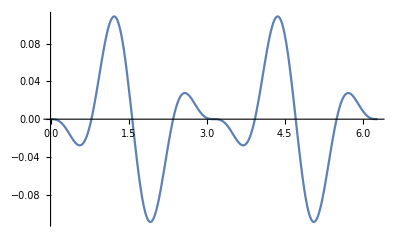

```mathematica
Plot[-1/4 (Cos[β]+Cos[3 β])  Sin[β]^3,{β,0,2π}]
```

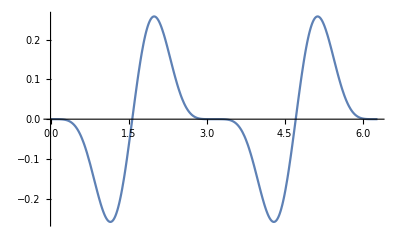

```mathematica
Plot[-1/8 Sin[2β](1-Cos[2 β])^2,{β,0,2π}]
```

```mathematica
Plot[-1/2 Sin[2β] Sin[β]^4,{β,0,2π}]
```

-Graphics-

```mathematica
zz=1/4 (-1-Cos[ξ]^2 (Cos[2 q]+2 Cos[2 β] Sin[q]^2)-Sin[ξ]^2)
```

1/4 (-1-Cos[ξ]^2 (Cos[2 q]+2 Cos[2 β] Sin[q]^2)-Sin[ξ]^2)

```mathematica
1-Cos[2β]==2Sin[β]^2//FullSimplify
```

True

```mathematica
TimeUsed[]
```

1979.95